```mathematica
SymbolToInt[s_]:=FromDigits[StringDrop[SymbolName[s],1]]
```

```mathematica
RecordToCouples[list_]:=Map[ToString[SymbolToInt[#[[1]]]]<>"-"<> ToString[ #[[2]]]&,list]
```

```mathematica
Haccumulate[list_]:=Block[{result={},i},
For[i=1,i≤Length[list],i++,
AppendTo[result,StringRiffle[Take[list,i],"#"]]
];
result]
```

```mathematica
Map[ToString[#]&,Haccumulate[{"1-1","3-2","4-3","5-2","6-3","7-2","8-1","9-3","10-1","11-4","12-1","13-4","14-1","15-3","16-4","17-3","18-2","19-1","20-2","21-2","22-4","23-1","24-4","25-3"}]]
```

{1-1,1-1#3-2,1-1#3-2#4-3,1-1#3-2#4-3#5-2,1-1#3-2#4-3#5-2#6-3,1-1#3-2#4-3#5-2#6-3#7-2,1-1#3-2#4-3#5-2#6-3#7-2#8-1,1-1#3-2#4-3#5-2#6-3#7-2#8-1#9-3,1-1#3-2#4-3#5-2#6-3#7-2#8-1#9-3#10-1,1-1#3-2#4-3#5-2#6-3#7-2#8-1#9-3#10-1#11-4,1-1#3-2#4-3#5-2#6-3#7-2#8-1#9-3#10-1#11-4#12-1,1-1#3-2#4-3#5-2#6-3#7-2#8-1#9-3#10-1#11-4#12-1#13-4,1-1#3-2#4-3#5-2#6-3#7-2#8-1#9-3#10-1#11-4#12-1#13-4#14-1,1-1#3-2#4-3#5-2#6-3#7-2#8-1#9-3#10-1#11-4#12-1#13-4#14-1#15-3,1-1#3-2#4-3#5-2#6-3#7-2#8-1#9-3#10-1#11-4#12-1#13-4#14-1#15-3#16-4,1-1#3-2#4-3#5-2#6-3#7-2#8-1#9-3#10-1#11-4#12-1#13-4#14-1#15-3#16-4#17-3,1-1#3-2#4-3#5-2#6-3#7-2#8-1#9-3#10-1#11-4#12-1#13-4#14-1#15-3#16-4#17-3#18-2,1-1#3-2#4-3#5-2#6-3#7-2#8-1#9-3#10-1#11-4#12-1#13-4#14-1#15-3#16-4#17-3#18-2#19-1,1-1#3-2#4-3#5-2#6-3#7-2#8-1#9-3#10-1#11-4#12-1#13-4#14-1#15-3#16-4#17-3#18-2#19-1#20-2,1-1#3-2#4-3#5-2#6-3#7-2#8-1#9-3#10-1#11-4#12-1#13-4#14-1#15-3#16-4#17-3#18-2#19-1#20-2#21-2,1-1#3-2#4-3#5-2#6-3#7-2#8-1#9-3#10-1#11-4#12-1#13-4#14-1#15-3#16-4#17-3#18-2#19-1#20-2#21-2#22-4,1-1#3-2#4-3#5-2#6-3#7-2#8-1#9-3#10-1#11-4#12-1#13-4#14-1#15-3#16-4#17-3#18-2#19-1#20-2#21-2#22-4#23-1,1-1#3-2#4-3#5-2#6-3#7-2#8-1#9-3#10-1#11-4#12-1#13-4#14-1#15-3#16-4#17-3#18-2#19-1#20-2#21-2#22-4#23-1#24-4,1-1#3-2#4-3#5-2#6-3#7-2#8-1#9-3#10-1#11-4#12-1#13-4#14-1#15-3#16-4#17-3#18-2#19-1#20-2#21-2#22-4#23-1#24-4#25-3}

```mathematica
RecordToCouples[{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->1,x11->4,x12->1,x13->4,x14->1,x15->3,x16->4,x17->3,x18->2,x19->1,x20->2,x21->2,x22->4,x23->1,x24->4,x25->3}]
```

{1-1,3-2,4-3,5-2,6-3,7-2,8-1,9-3,10-1,11-4,12-1,13-4,14-1,15-3,16-4,17-3,18-2,19-1,20-2,21-2,22-4,23-1,24-4,25-3}

```mathematica
With[
{k=24534},
FindHamiltonianPath[Graph[plantri[[k]]],1,VertexCount[Graph[plantri[[k]]]]]//Timing
]
```

{0.03125,{1,5,4,3,10,21,11,12,6,13,9,20,19,18,8,2,7,14,22,15,16,17,24,23,25}}

```mathematica
orderrrr=Map[Symbol["x"<>ToString[#]]&, {1,5,4,3,10,21,11,12,6,13,9,20,19,18,8,7,14,22,15,16,17,24,23,25}]
```

{x1,x5,x4,x3,x10,x21,x11,x12,x6,x13,x9,x20,x19,x18,x8,x7,x14,x22,x15,x16,x17,x24,x23,x25}

```mathematica
orderrrr/.{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->1,x11->4,x12->1,x13->4,x14->1,x15->3,x16->4,x17->3,x18->2,x19->1,x20->2,x21->2,x22->4,x23->1,x24->4,x25->3}
```

{1,2,3,2,1,2,4,1,3,4,3,2,1,2,1,2,1,4,3,4,3,4,1,3}

```mathematica
edges=Map[EdgeList[PathGraph[Map[ToString[#]&,Haccumulate[ orderrrr/.#]]]]&,
{{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->1,x11->4,x12->1,x13->4,x14->1,x15->3,x16->4,x17->3,x18->2,x19->1,x20->2,x21->2,x22->4,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->1,x11->4,x12->1,x13->4,x14->1,x15->3,x16->4,x17->3,x18->2,x19->1,x20->2,x21->2,x22->4,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->1,x11->4,x12->1,x13->4,x14->1,x15->3,x16->4,x17->3,x18->2,x19->1,x20->4,x21->2,x22->2,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->1,x11->4,x12->1,x13->4,x14->1,x15->3,x16->4,x17->3,x18->2,x19->4,x20->2,x21->2,x22->4,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->1,x11->4,x12->1,x13->4,x14->1,x15->3,x16->4,x17->3,x18->4,x19->1,x20->2,x21->2,x22->4,x23->1,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->1,x11->4,x12->1,x13->4,x14->1,x15->3,x16->4,x17->3,x18->4,x19->1,x20->4,x21->2,x22->2,x23->1,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->1,x11->4,x12->1,x13->4,x14->1,x15->4,x16->3,x17->2,x18->4,x19->1,x20->2,x21->2,x22->3,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->1,x11->4,x12->1,x13->4,x14->1,x15->4,x16->3,x17->2,x18->4,x19->1,x20->4,x21->2,x22->3,x23->1,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->1,x11->4,x12->1,x13->4,x14->1,x15->4,x16->3,x17->4,x18->2,x19->1,x20->2,x21->2,x22->3,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->1,x11->4,x12->1,x13->4,x14->1,x15->4,x16->3,x17->4,x18->2,x19->1,x20->2,x21->2,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->1,x11->4,x12->1,x13->4,x14->1,x15->4,x16->3,x17->4,x18->2,x19->1,x20->4,x21->2,x22->3,x23->1,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->1,x11->4,x12->1,x13->4,x14->1,x15->4,x16->3,x17->4,x18->2,x19->4,x20->2,x21->2,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->1,x11->4,x12->1,x13->4,x14->4,x15->1,x16->3,x17->2,x18->4,x19->2,x20->1,x21->2,x22->2,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->1,x11->4,x12->1,x13->4,x14->4,x15->1,x16->3,x17->4,x18->2,x19->1,x20->2,x21->2,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->1,x11->4,x12->1,x13->4,x14->4,x15->1,x16->3,x17->4,x18->2,x19->4,x20->2,x21->2,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->1,x11->4,x12->1,x13->4,x14->4,x15->1,x16->4,x17->2,x18->4,x19->2,x20->1,x21->2,x22->2,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->1,x11->4,x12->1,x13->4,x14->4,x15->1,x16->4,x17->3,x18->4,x19->2,x20->1,x21->2,x22->3,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->1,x11->4,x12->1,x13->4,x14->4,x15->3,x16->4,x17->2,x18->4,x19->2,x20->1,x21->2,x22->2,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->1,x11->4,x12->1,x13->4,x14->4,x15->3,x16->4,x17->3,x18->2,x19->1,x20->2,x21->2,x22->1,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->1,x11->4,x12->1,x13->4,x14->4,x15->3,x16->4,x17->3,x18->2,x19->4,x20->2,x21->2,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->3,x16->4,x17->3,x18->2,x19->1,x20->2,x21->2,x22->4,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->3,x16->4,x17->3,x18->2,x19->1,x20->2,x21->2,x22->4,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->3,x16->4,x17->3,x18->2,x19->1,x20->4,x21->2,x22->2,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->3,x16->4,x17->3,x18->2,x19->4,x20->2,x21->2,x22->4,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->3,x16->4,x17->3,x18->4,x19->1,x20->2,x21->2,x22->4,x23->1,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->3,x16->4,x17->3,x18->4,x19->1,x20->4,x21->2,x22->2,x23->1,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->4,x16->3,x17->2,x18->4,x19->1,x20->2,x21->2,x22->3,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->4,x16->3,x17->2,x18->4,x19->1,x20->4,x21->2,x22->3,x23->1,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->4,x16->3,x17->4,x18->2,x19->1,x20->2,x21->2,x22->3,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->4,x16->3,x17->4,x18->2,x19->1,x20->2,x21->2,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->4,x16->3,x17->4,x18->2,x19->1,x20->4,x21->2,x22->3,x23->1,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->4,x16->3,x17->4,x18->2,x19->4,x20->2,x21->2,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->4,x15->1,x16->3,x17->2,x18->4,x19->2,x20->1,x21->2,x22->2,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->4,x15->1,x16->3,x17->4,x18->2,x19->1,x20->2,x21->2,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->4,x15->1,x16->3,x17->4,x18->2,x19->4,x20->2,x21->2,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->4,x15->1,x16->4,x17->2,x18->4,x19->2,x20->1,x21->2,x22->2,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->4,x15->1,x16->4,x17->3,x18->4,x19->2,x20->1,x21->2,x22->3,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->4,x15->3,x16->4,x17->2,x18->4,x19->2,x20->1,x21->2,x22->2,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->4,x15->3,x16->4,x17->3,x18->2,x19->1,x20->2,x21->2,x22->1,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->4,x15->3,x16->4,x17->3,x18->2,x19->4,x20->2,x21->2,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->1,x11->4,x12->1,x13->4,x14->1,x15->3,x16->1,x17->2,x18->1,x19->2,x20->4,x21->2,x22->2,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->1,x11->4,x12->1,x13->4,x14->1,x15->3,x16->1,x17->3,x18->2,x19->1,x20->2,x21->2,x22->4,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->1,x11->4,x12->1,x13->4,x14->1,x15->3,x16->1,x17->3,x18->2,x19->4,x20->2,x21->2,x22->4,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->1,x11->4,x12->1,x13->4,x14->1,x15->4,x16->1,x17->2,x18->1,x19->2,x20->4,x21->2,x22->2,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->1,x11->4,x12->1,x13->4,x14->1,x15->4,x16->1,x17->3,x18->1,x19->2,x20->4,x21->2,x22->3,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->1,x11->4,x12->1,x13->4,x14->1,x15->4,x16->3,x17->1,x18->2,x19->1,x20->2,x21->2,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->1,x11->4,x12->1,x13->4,x14->1,x15->4,x16->3,x17->1,x18->2,x19->4,x20->2,x21->2,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->1,x11->4,x12->1,x13->4,x14->1,x15->4,x16->3,x17->2,x18->1,x19->2,x20->4,x21->2,x22->2,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->1,x11->4,x12->1,x13->4,x14->4,x15->1,x16->3,x17->1,x18->2,x19->1,x20->2,x21->2,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->1,x11->4,x12->1,x13->4,x14->4,x15->1,x16->3,x17->1,x18->2,x19->4,x20->1,x21->2,x22->3,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->1,x11->4,x12->1,x13->4,x14->4,x15->1,x16->3,x17->1,x18->2,x19->4,x20->2,x21->2,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->1,x11->4,x12->1,x13->4,x14->4,x15->1,x16->3,x17->1,x18->2,x19->4,x20->2,x21->2,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->1,x11->4,x12->1,x13->4,x14->4,x15->1,x16->3,x17->2,x18->1,x19->4,x20->1,x21->2,x22->3,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->1,x11->4,x12->1,x13->4,x14->4,x15->1,x16->3,x17->2,x18->1,x19->4,x20->2,x21->2,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->1,x11->4,x12->1,x13->4,x14->4,x15->3,x16->1,x17->3,x18->1,x19->4,x20->1,x21->2,x22->2,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->1,x11->4,x12->1,x13->4,x14->4,x15->3,x16->1,x17->3,x18->1,x19->4,x20->2,x21->2,x22->1,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->1,x11->4,x12->1,x13->4,x14->4,x15->3,x16->1,x17->3,x18->2,x19->1,x20->2,x21->2,x22->1,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->1,x11->4,x12->1,x13->4,x14->4,x15->3,x16->1,x17->3,x18->2,x19->4,x20->1,x21->2,x22->2,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->1,x11->4,x12->1,x13->4,x14->4,x15->3,x16->1,x17->3,x18->2,x19->4,x20->2,x21->2,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->1,x11->4,x12->1,x13->4,x14->4,x15->3,x16->1,x17->3,x18->2,x19->4,x20->2,x21->2,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->3,x16->1,x17->2,x18->1,x19->2,x20->4,x21->2,x22->2,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->3,x16->1,x17->3,x18->2,x19->1,x20->2,x21->2,x22->4,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->3,x16->1,x17->3,x18->2,x19->4,x20->2,x21->2,x22->4,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->4,x16->1,x17->2,x18->1,x19->2,x20->4,x21->2,x22->2,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->4,x16->1,x17->3,x18->1,x19->2,x20->4,x21->2,x22->3,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->4,x16->3,x17->1,x18->2,x19->1,x20->2,x21->2,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->4,x16->3,x17->1,x18->2,x19->4,x20->2,x21->2,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->4,x16->3,x17->2,x18->1,x19->2,x20->4,x21->2,x22->2,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->4,x11->1,x12->4,x13->1,x14->4,x15->1,x16->3,x17->1,x18->2,x19->1,x20->2,x21->2,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->4,x11->1,x12->4,x13->1,x14->4,x15->1,x16->3,x17->1,x18->2,x19->4,x20->1,x21->2,x22->3,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->4,x11->1,x12->4,x13->1,x14->4,x15->1,x16->3,x17->1,x18->2,x19->4,x20->2,x21->2,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->4,x11->1,x12->4,x13->1,x14->4,x15->1,x16->3,x17->1,x18->2,x19->4,x20->2,x21->2,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->4,x11->1,x12->4,x13->1,x14->4,x15->1,x16->3,x17->2,x18->1,x19->4,x20->1,x21->2,x22->3,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->4,x11->1,x12->4,x13->1,x14->4,x15->1,x16->3,x17->2,x18->1,x19->4,x20->2,x21->2,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->4,x11->1,x12->4,x13->1,x14->4,x15->3,x16->1,x17->3,x18->1,x19->4,x20->1,x21->2,x22->2,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->4,x11->1,x12->4,x13->1,x14->4,x15->3,x16->1,x17->3,x18->1,x19->4,x20->2,x21->2,x22->1,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->4,x11->1,x12->4,x13->1,x14->4,x15->3,x16->1,x17->3,x18->2,x19->1,x20->2,x21->2,x22->1,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->4,x11->1,x12->4,x13->1,x14->4,x15->3,x16->1,x17->3,x18->2,x19->4,x20->1,x21->2,x22->2,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->4,x11->1,x12->4,x13->1,x14->4,x15->3,x16->1,x17->3,x18->2,x19->4,x20->2,x21->2,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->2,x8->4,x9->3,x10->4,x11->1,x12->4,x13->1,x14->4,x15->3,x16->1,x17->3,x18->2,x19->4,x20->2,x21->2,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->2,x16->3,x17->2,x18->4,x19->1,x20->2,x21->2,x22->3,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->2,x16->3,x17->2,x18->4,x19->1,x20->4,x21->2,x22->3,x23->1,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->2,x16->3,x17->2,x18->4,x19->1,x20->4,x21->2,x22->3,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->2,x16->3,x17->2,x18->4,x19->2,x20->4,x21->2,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->2,x16->3,x17->4,x18->2,x19->1,x20->2,x21->2,x22->3,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->2,x16->3,x17->4,x18->2,x19->1,x20->4,x21->2,x22->3,x23->1,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->3,x16->2,x17->3,x18->2,x19->1,x20->2,x21->2,x22->4,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->3,x16->2,x17->3,x18->2,x19->1,x20->4,x21->2,x22->2,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->3,x16->2,x17->3,x18->4,x19->1,x20->2,x21->2,x22->4,x23->1,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->3,x16->2,x17->3,x18->4,x19->1,x20->4,x21->2,x22->2,x23->1,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->3,x16->2,x17->3,x18->4,x19->1,x20->4,x21->2,x22->2,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->3,x16->2,x17->3,x18->4,x19->2,x20->4,x21->2,x22->2,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->2,x15->1,x16->2,x17->3,x18->2,x19->4,x20->1,x21->2,x22->3,x23->4,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->2,x15->1,x16->2,x17->4,x18->2,x19->4,x20->1,x21->2,x22->4,x23->3,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->2,x15->1,x16->3,x17->2,x18->4,x19->1,x20->4,x21->2,x22->3,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->2,x15->1,x16->3,x17->2,x18->4,x19->2,x20->4,x21->2,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->2,x15->1,x16->3,x17->4,x18->2,x19->4,x20->1,x21->2,x22->4,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->2,x15->3,x16->2,x17->3,x18->4,x19->1,x20->4,x21->2,x22->1,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->2,x15->3,x16->2,x17->3,x18->4,x19->2,x20->4,x21->2,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->1,x9->3,x10->4,x11->1,x12->4,x13->1,x14->2,x15->3,x16->2,x17->4,x18->2,x19->4,x20->1,x21->2,x22->4,x23->1,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->1,x10->4,x11->1,x12->4,x13->2,x14->2,x15->1,x16->3,x17->1,x18->3,x19->2,x20->3,x21->3,x22->4,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->1,x10->4,x11->1,x12->4,x13->2,x14->2,x15->1,x16->3,x17->1,x18->3,x19->2,x20->4,x21->3,x22->3,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->1,x10->4,x11->1,x12->4,x13->2,x14->2,x15->1,x16->3,x17->1,x18->4,x19->2,x20->3,x21->3,x22->4,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->1,x10->4,x11->1,x12->4,x13->2,x14->2,x15->1,x16->3,x17->1,x18->4,x19->2,x20->4,x21->3,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->1,x10->4,x11->1,x12->4,x13->2,x14->2,x15->1,x16->3,x17->1,x18->4,x19->2,x20->4,x21->3,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->1,x10->4,x11->1,x12->4,x13->2,x14->2,x15->1,x16->3,x17->1,x18->4,x19->3,x20->4,x21->3,x22->3,x23->4,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->1,x10->4,x11->1,x12->4,x13->2,x14->2,x15->3,x16->1,x17->3,x18->4,x19->2,x20->3,x21->3,x22->1,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->1,x10->4,x11->1,x12->4,x13->2,x14->2,x15->3,x16->1,x17->3,x18->4,x19->2,x20->4,x21->3,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->1,x10->4,x11->1,x12->4,x13->2,x14->2,x15->3,x16->1,x17->3,x18->4,x19->2,x20->4,x21->3,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->1,x10->4,x11->1,x12->4,x13->2,x14->2,x15->3,x16->1,x17->3,x18->4,x19->3,x20->4,x21->3,x22->1,x23->4,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->1,x10->4,x11->1,x12->4,x13->2,x14->2,x15->3,x16->1,x17->4,x18->3,x19->2,x20->3,x21->3,x22->1,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->1,x10->4,x11->1,x12->4,x13->2,x14->2,x15->3,x16->1,x17->4,x18->3,x19->2,x20->4,x21->3,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->1,x10->4,x11->1,x12->4,x13->2,x14->3,x15->1,x16->3,x17->1,x18->4,x19->2,x20->4,x21->3,x22->2,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->1,x10->4,x11->1,x12->4,x13->2,x14->3,x15->1,x16->3,x17->1,x18->4,x19->3,x20->4,x21->3,x22->2,x23->4,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->1,x10->4,x11->1,x12->4,x13->2,x14->3,x15->1,x16->3,x17->4,x18->3,x19->4,x20->2,x21->3,x22->4,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->1,x10->4,x11->1,x12->4,x13->2,x14->3,x15->2,x16->1,x17->3,x18->4,x19->2,x20->4,x21->3,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->1,x10->4,x11->1,x12->4,x13->2,x14->3,x15->2,x16->1,x17->3,x18->4,x19->3,x20->4,x21->3,x22->1,x23->4,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->1,x10->4,x11->1,x12->4,x13->2,x14->3,x15->2,x16->1,x17->4,x18->3,x19->4,x20->2,x21->3,x22->4,x23->3,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->1,x10->4,x11->1,x12->4,x13->2,x14->3,x15->2,x16->3,x17->1,x18->3,x19->4,x20->2,x21->3,x22->1,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->1,x10->4,x11->1,x12->4,x13->2,x14->3,x15->2,x16->3,x17->4,x18->3,x19->4,x20->2,x21->3,x22->4,x23->1,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->2,x16->1,x17->3,x18->1,x19->4,x20->2,x21->2,x22->3,x23->4,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->2,x16->1,x17->4,x18->1,x19->4,x20->2,x21->2,x22->4,x23->3,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->2,x16->3,x17->1,x18->4,x19->1,x20->4,x21->2,x22->3,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->2,x16->3,x17->1,x18->4,x19->2,x20->4,x21->2,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->2,x16->3,x17->4,x18->1,x19->4,x20->2,x21->2,x22->4,x23->1,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->3,x16->1,x17->3,x18->4,x19->1,x20->4,x21->2,x22->2,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->3,x16->1,x17->3,x18->4,x19->2,x20->4,x21->2,x22->2,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->3,x10->4,x11->1,x12->4,x13->1,x14->1,x15->3,x16->1,x17->4,x18->1,x19->4,x20->2,x21->2,x22->4,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->3,x10->4,x11->1,x12->4,x13->1,x14->2,x15->1,x16->3,x17->1,x18->4,x19->1,x20->4,x21->2,x22->3,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->3,x10->4,x11->1,x12->4,x13->1,x14->2,x15->1,x16->3,x17->1,x18->4,x19->2,x20->1,x21->2,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->3,x10->4,x11->1,x12->4,x13->1,x14->2,x15->1,x16->3,x17->1,x18->4,x19->2,x20->4,x21->2,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->3,x10->4,x11->1,x12->4,x13->1,x14->2,x15->1,x16->3,x17->1,x18->4,x19->2,x20->4,x21->2,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->3,x10->4,x11->1,x12->4,x13->1,x14->2,x15->1,x16->3,x17->4,x18->1,x19->2,x20->1,x21->2,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->3,x10->4,x11->1,x12->4,x13->1,x14->2,x15->1,x16->3,x17->4,x18->1,x19->2,x20->4,x21->2,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->3,x10->4,x11->1,x12->4,x13->1,x14->2,x15->3,x16->1,x17->3,x18->1,x19->2,x20->1,x21->2,x22->4,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->3,x10->4,x11->1,x12->4,x13->1,x14->2,x15->3,x16->1,x17->3,x18->1,x19->2,x20->4,x21->2,x22->1,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->3,x10->4,x11->1,x12->4,x13->1,x14->2,x15->3,x16->1,x17->3,x18->4,x19->1,x20->4,x21->2,x22->1,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->3,x10->4,x11->1,x12->4,x13->1,x14->2,x15->3,x16->1,x17->3,x18->4,x19->2,x20->1,x21->2,x22->4,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->3,x10->4,x11->1,x12->4,x13->1,x14->2,x15->3,x16->1,x17->3,x18->4,x19->2,x20->4,x21->2,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->2,x9->3,x10->4,x11->1,x12->4,x13->1,x14->2,x15->3,x16->1,x17->3,x18->4,x19->2,x20->4,x21->2,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->3,x9->1,x10->4,x11->1,x12->4,x13->2,x14->2,x15->1,x16->2,x17->1,x18->4,x19->2,x20->4,x21->3,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->3,x9->1,x10->4,x11->1,x12->4,x13->2,x14->2,x15->1,x16->2,x17->1,x18->4,x19->3,x20->4,x21->3,x22->3,x23->4,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->3,x9->1,x10->4,x11->1,x12->4,x13->2,x14->2,x15->1,x16->2,x17->4,x18->2,x19->4,x20->3,x21->3,x22->4,x23->3,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->3,x9->1,x10->4,x11->1,x12->4,x13->2,x14->2,x15->3,x16->1,x17->2,x18->4,x19->2,x20->4,x21->3,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->3,x9->1,x10->4,x11->1,x12->4,x13->2,x14->2,x15->3,x16->1,x17->2,x18->4,x19->3,x20->4,x21->3,x22->1,x23->4,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->3,x9->1,x10->4,x11->1,x12->4,x13->2,x14->2,x15->3,x16->1,x17->4,x18->2,x19->4,x20->3,x21->3,x22->4,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->3,x9->1,x10->4,x11->1,x12->4,x13->2,x14->2,x15->3,x16->2,x17->1,x18->2,x19->4,x20->3,x21->3,x22->1,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->3,x9->1,x10->4,x11->1,x12->4,x13->2,x14->2,x15->3,x16->2,x17->4,x18->2,x19->4,x20->3,x21->3,x22->4,x23->1,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->3,x9->1,x10->4,x11->1,x12->4,x13->2,x14->3,x15->1,x16->2,x17->1,x18->2,x19->3,x20->2,x21->3,x22->4,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->3,x9->1,x10->4,x11->1,x12->4,x13->2,x14->3,x15->1,x16->2,x17->1,x18->2,x19->3,x20->4,x21->3,x22->2,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->3,x9->1,x10->4,x11->1,x12->4,x13->2,x14->3,x15->1,x16->2,x17->1,x18->4,x19->2,x20->4,x21->3,x22->2,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->3,x9->1,x10->4,x11->1,x12->4,x13->2,x14->3,x15->1,x16->2,x17->1,x18->4,x19->3,x20->2,x21->3,x22->4,x23->3,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->3,x9->1,x10->4,x11->1,x12->4,x13->2,x14->3,x15->1,x16->2,x17->1,x18->4,x19->3,x20->4,x21->3,x22->2,x23->3,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->3,x9->1,x10->4,x11->1,x12->4,x13->2,x14->3,x15->1,x16->2,x17->1,x18->4,x19->3,x20->4,x21->3,x22->2,x23->4,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->3,x9->1,x10->4,x11->1,x12->4,x13->2,x14->3,x15->2,x16->1,x17->2,x18->4,x19->2,x20->4,x21->3,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->3,x9->1,x10->4,x11->1,x12->4,x13->2,x14->3,x15->2,x16->1,x17->2,x18->4,x19->3,x20->2,x21->3,x22->1,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->3,x9->1,x10->4,x11->1,x12->4,x13->2,x14->3,x15->2,x16->1,x17->2,x18->4,x19->3,x20->4,x21->3,x22->1,x23->3,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->3,x9->1,x10->4,x11->1,x12->4,x13->2,x14->3,x15->2,x16->1,x17->2,x18->4,x19->3,x20->4,x21->3,x22->1,x23->4,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->3,x9->1,x10->4,x11->1,x12->4,x13->2,x14->3,x15->2,x16->1,x17->4,x18->2,x19->3,x20->2,x21->3,x22->1,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->3,x7->4,x8->3,x9->1,x10->4,x11->1,x12->4,x13->2,x14->3,x15->2,x16->1,x17->4,x18->2,x19->3,x20->4,x21->3,x22->1,x23->3,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->1,x11->4,x12->3,x13->1,x14->1,x15->3,x16->4,x17->3,x18->2,x19->1,x20->2,x21->2,x22->4,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->1,x11->4,x12->3,x13->1,x14->1,x15->3,x16->4,x17->3,x18->2,x19->1,x20->2,x21->2,x22->4,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->1,x11->4,x12->3,x13->1,x14->1,x15->3,x16->4,x17->3,x18->2,x19->1,x20->4,x21->2,x22->2,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->1,x11->4,x12->3,x13->1,x14->1,x15->3,x16->4,x17->3,x18->2,x19->4,x20->2,x21->2,x22->4,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->1,x11->4,x12->3,x13->1,x14->1,x15->3,x16->4,x17->3,x18->4,x19->1,x20->2,x21->2,x22->4,x23->1,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->1,x11->4,x12->3,x13->1,x14->1,x15->3,x16->4,x17->3,x18->4,x19->1,x20->4,x21->2,x22->2,x23->1,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->3,x17->2,x18->4,x19->1,x20->2,x21->2,x22->3,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->3,x17->2,x18->4,x19->1,x20->4,x21->2,x22->3,x23->1,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->3,x17->4,x18->2,x19->1,x20->2,x21->2,x22->3,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->3,x17->4,x18->2,x19->1,x20->2,x21->2,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->3,x17->4,x18->2,x19->1,x20->4,x21->2,x22->3,x23->1,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->3,x17->4,x18->2,x19->4,x20->2,x21->2,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->1,x11->4,x12->3,x13->1,x14->4,x15->1,x16->3,x17->2,x18->4,x19->2,x20->1,x21->2,x22->2,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->1,x11->4,x12->3,x13->1,x14->4,x15->1,x16->3,x17->4,x18->2,x19->1,x20->2,x21->2,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->1,x11->4,x12->3,x13->1,x14->4,x15->1,x16->3,x17->4,x18->2,x19->4,x20->2,x21->2,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->1,x11->4,x12->3,x13->1,x14->4,x15->1,x16->4,x17->2,x18->4,x19->2,x20->1,x21->2,x22->2,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->1,x11->4,x12->3,x13->1,x14->4,x15->1,x16->4,x17->3,x18->4,x19->2,x20->1,x21->2,x22->3,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->1,x11->4,x12->3,x13->1,x14->4,x15->3,x16->4,x17->2,x18->4,x19->2,x20->1,x21->2,x22->2,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->1,x11->4,x12->3,x13->1,x14->4,x15->3,x16->4,x17->3,x18->2,x19->1,x20->2,x21->2,x22->1,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->1,x11->4,x12->3,x13->1,x14->4,x15->3,x16->4,x17->3,x18->2,x19->4,x20->2,x21->2,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->3,x16->4,x17->3,x18->2,x19->1,x20->2,x21->2,x22->4,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->3,x16->4,x17->3,x18->2,x19->1,x20->2,x21->2,x22->4,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->3,x16->4,x17->3,x18->2,x19->1,x20->4,x21->2,x22->2,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->3,x16->4,x17->3,x18->2,x19->4,x20->2,x21->2,x22->4,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->3,x16->4,x17->3,x18->4,x19->1,x20->2,x21->2,x22->4,x23->1,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->3,x16->4,x17->3,x18->4,x19->1,x20->4,x21->2,x22->2,x23->1,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->4,x16->3,x17->2,x18->4,x19->1,x20->2,x21->2,x22->3,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->4,x16->3,x17->2,x18->4,x19->1,x20->4,x21->2,x22->3,x23->1,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->4,x16->3,x17->4,x18->2,x19->1,x20->2,x21->2,x22->3,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->4,x16->3,x17->4,x18->2,x19->1,x20->2,x21->2,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->4,x16->3,x17->4,x18->2,x19->1,x20->4,x21->2,x22->3,x23->1,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->4,x16->3,x17->4,x18->2,x19->4,x20->2,x21->2,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->4,x15->1,x16->3,x17->2,x18->4,x19->2,x20->1,x21->2,x22->2,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->4,x15->1,x16->3,x17->4,x18->2,x19->1,x20->2,x21->2,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->4,x15->1,x16->3,x17->4,x18->2,x19->4,x20->2,x21->2,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->4,x15->1,x16->4,x17->2,x18->4,x19->2,x20->1,x21->2,x22->2,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->4,x15->1,x16->4,x17->3,x18->4,x19->2,x20->1,x21->2,x22->3,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->4,x15->3,x16->4,x17->2,x18->4,x19->2,x20->1,x21->2,x22->2,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->4,x15->3,x16->4,x17->3,x18->2,x19->1,x20->2,x21->2,x22->1,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->4,x15->3,x16->4,x17->3,x18->2,x19->4,x20->2,x21->2,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->1,x13->3,x14->1,x15->3,x16->4,x17->2,x18->3,x19->1,x20->2,x21->2,x22->4,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->1,x13->3,x14->1,x15->3,x16->4,x17->2,x18->3,x19->1,x20->3,x21->2,x22->4,x23->1,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->1,x13->3,x14->1,x15->3,x16->4,x17->3,x18->2,x19->1,x20->2,x21->2,x22->4,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->1,x13->3,x14->1,x15->3,x16->4,x17->3,x18->2,x19->1,x20->2,x21->2,x22->4,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->1,x13->3,x14->1,x15->3,x16->4,x17->3,x18->2,x19->1,x20->3,x21->2,x22->4,x23->1,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->1,x13->3,x14->1,x15->3,x16->4,x17->3,x18->2,x19->3,x20->2,x21->2,x22->4,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->1,x13->3,x14->1,x15->4,x16->3,x17->4,x18->2,x19->1,x20->2,x21->2,x22->3,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->1,x13->3,x14->1,x15->4,x16->3,x17->4,x18->2,x19->1,x20->2,x21->2,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->1,x13->3,x14->1,x15->4,x16->3,x17->4,x18->2,x19->1,x20->3,x21->2,x22->2,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->1,x13->3,x14->1,x15->4,x16->3,x17->4,x18->2,x19->3,x20->2,x21->2,x22->3,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->1,x13->3,x14->1,x15->4,x16->3,x17->4,x18->3,x19->1,x20->2,x21->2,x22->3,x23->1,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->1,x13->3,x14->1,x15->4,x16->3,x17->4,x18->3,x19->1,x20->3,x21->2,x22->2,x23->1,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->1,x13->3,x14->3,x15->1,x16->3,x17->2,x18->3,x19->2,x20->1,x21->2,x22->2,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->1,x13->3,x14->3,x15->1,x16->3,x17->4,x18->3,x19->2,x20->1,x21->2,x22->4,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->1,x13->3,x14->3,x15->1,x16->4,x17->2,x18->3,x19->2,x20->1,x21->2,x22->2,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->1,x13->3,x14->3,x15->1,x16->4,x17->3,x18->2,x19->1,x20->2,x21->2,x22->4,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->1,x13->3,x14->3,x15->1,x16->4,x17->3,x18->2,x19->3,x20->2,x21->2,x22->4,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->1,x13->3,x14->3,x15->4,x16->3,x17->2,x18->3,x19->2,x20->1,x21->2,x22->2,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->1,x13->3,x14->3,x15->4,x16->3,x17->4,x18->2,x19->1,x20->2,x21->2,x22->1,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->1,x13->3,x14->3,x15->4,x16->3,x17->4,x18->2,x19->3,x20->2,x21->2,x22->1,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->3,x16->4,x17->2,x18->3,x19->1,x20->2,x21->2,x22->4,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->3,x16->4,x17->2,x18->3,x19->1,x20->3,x21->2,x22->4,x23->1,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->3,x16->4,x17->3,x18->2,x19->1,x20->2,x21->2,x22->4,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->3,x16->4,x17->3,x18->2,x19->1,x20->2,x21->2,x22->4,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->3,x16->4,x17->3,x18->2,x19->1,x20->3,x21->2,x22->4,x23->1,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->3,x16->4,x17->3,x18->2,x19->3,x20->2,x21->2,x22->4,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->3,x17->4,x18->2,x19->1,x20->2,x21->2,x22->3,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->3,x17->4,x18->2,x19->1,x20->2,x21->2,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->3,x17->4,x18->2,x19->1,x20->3,x21->2,x22->2,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->3,x17->4,x18->2,x19->3,x20->2,x21->2,x22->3,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->3,x17->4,x18->3,x19->1,x20->2,x21->2,x22->3,x23->1,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->3,x17->4,x18->3,x19->1,x20->3,x21->2,x22->2,x23->1,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->3,x15->1,x16->3,x17->2,x18->3,x19->2,x20->1,x21->2,x22->2,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->3,x15->1,x16->3,x17->4,x18->3,x19->2,x20->1,x21->2,x22->4,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->3,x15->1,x16->4,x17->2,x18->3,x19->2,x20->1,x21->2,x22->2,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->3,x15->1,x16->4,x17->3,x18->2,x19->1,x20->2,x21->2,x22->4,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->3,x15->1,x16->4,x17->3,x18->2,x19->3,x20->2,x21->2,x22->4,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->3,x15->4,x16->3,x17->2,x18->3,x19->2,x20->1,x21->2,x22->2,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->3,x15->4,x16->3,x17->4,x18->2,x19->1,x20->2,x21->2,x22->1,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->3,x15->4,x16->3,x17->4,x18->2,x19->3,x20->2,x21->2,x22->1,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->1,x13->3,x14->1,x15->3,x16->1,x17->2,x18->1,x19->2,x20->3,x21->2,x22->2,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->1,x13->3,x14->1,x15->3,x16->1,x17->4,x18->1,x19->2,x20->3,x21->2,x22->4,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->1,x13->3,x14->1,x15->3,x16->4,x17->1,x18->2,x19->1,x20->2,x21->2,x22->4,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->1,x13->3,x14->1,x15->3,x16->4,x17->1,x18->2,x19->3,x20->2,x21->2,x22->4,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->1,x13->3,x14->1,x15->3,x16->4,x17->2,x18->1,x19->2,x20->3,x21->2,x22->2,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->1,x13->3,x14->1,x15->4,x16->1,x17->2,x18->1,x19->2,x20->3,x21->2,x22->2,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->1,x13->3,x14->1,x15->4,x16->1,x17->4,x18->2,x19->1,x20->2,x21->2,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->1,x13->3,x14->1,x15->4,x16->1,x17->4,x18->2,x19->3,x20->2,x21->2,x22->3,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->1,x13->3,x14->3,x15->1,x16->4,x17->1,x18->2,x19->1,x20->2,x21->2,x22->4,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->1,x13->3,x14->3,x15->1,x16->4,x17->1,x18->2,x19->3,x20->1,x21->2,x22->4,x23->3,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->1,x13->3,x14->3,x15->1,x16->4,x17->1,x18->2,x19->3,x20->2,x21->2,x22->4,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->1,x13->3,x14->3,x15->1,x16->4,x17->1,x18->2,x19->3,x20->2,x21->2,x22->4,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->1,x13->3,x14->3,x15->1,x16->4,x17->2,x18->1,x19->3,x20->1,x21->2,x22->4,x23->3,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->1,x13->3,x14->3,x15->1,x16->4,x17->2,x18->1,x19->3,x20->2,x21->2,x22->4,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->1,x13->3,x14->3,x15->4,x16->1,x17->4,x18->1,x19->3,x20->1,x21->2,x22->2,x23->3,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->1,x13->3,x14->3,x15->4,x16->1,x17->4,x18->1,x19->3,x20->2,x21->2,x22->1,x23->3,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->1,x13->3,x14->3,x15->4,x16->1,x17->4,x18->2,x19->1,x20->2,x21->2,x22->1,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->1,x13->3,x14->3,x15->4,x16->1,x17->4,x18->2,x19->3,x20->1,x21->2,x22->2,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->1,x13->3,x14->3,x15->4,x16->1,x17->4,x18->2,x19->3,x20->2,x21->2,x22->1,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->1,x13->3,x14->3,x15->4,x16->1,x17->4,x18->2,x19->3,x20->2,x21->2,x22->1,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->3,x16->1,x17->2,x18->1,x19->2,x20->3,x21->2,x22->2,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->3,x16->1,x17->4,x18->1,x19->2,x20->3,x21->2,x22->4,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->3,x16->4,x17->1,x18->2,x19->1,x20->2,x21->2,x22->4,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->3,x16->4,x17->1,x18->2,x19->3,x20->2,x21->2,x22->4,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->3,x16->4,x17->2,x18->1,x19->2,x20->3,x21->2,x22->2,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->1,x17->2,x18->1,x19->2,x20->3,x21->2,x22->2,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->1,x17->4,x18->2,x19->1,x20->2,x21->2,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->1,x17->4,x18->2,x19->3,x20->2,x21->2,x22->3,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->3,x13->1,x14->3,x15->1,x16->4,x17->1,x18->2,x19->1,x20->2,x21->2,x22->4,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->3,x13->1,x14->3,x15->1,x16->4,x17->1,x18->2,x19->3,x20->1,x21->2,x22->4,x23->3,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->3,x13->1,x14->3,x15->1,x16->4,x17->1,x18->2,x19->3,x20->2,x21->2,x22->4,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->3,x13->1,x14->3,x15->1,x16->4,x17->1,x18->2,x19->3,x20->2,x21->2,x22->4,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->3,x13->1,x14->3,x15->1,x16->4,x17->2,x18->1,x19->3,x20->1,x21->2,x22->4,x23->3,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->3,x13->1,x14->3,x15->1,x16->4,x17->2,x18->1,x19->3,x20->2,x21->2,x22->4,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->3,x13->1,x14->3,x15->4,x16->1,x17->4,x18->1,x19->3,x20->1,x21->2,x22->2,x23->3,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->3,x13->1,x14->3,x15->4,x16->1,x17->4,x18->1,x19->3,x20->2,x21->2,x22->1,x23->3,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->3,x13->1,x14->3,x15->4,x16->1,x17->4,x18->2,x19->1,x20->2,x21->2,x22->1,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->3,x13->1,x14->3,x15->4,x16->1,x17->4,x18->2,x19->3,x20->1,x21->2,x22->2,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->3,x13->1,x14->3,x15->4,x16->1,x17->4,x18->2,x19->3,x20->2,x21->2,x22->1,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->3,x9->4,x10->1,x11->4,x12->3,x13->1,x14->3,x15->4,x16->1,x17->4,x18->2,x19->3,x20->2,x21->2,x22->1,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->1,x11->4,x12->3,x13->1,x14->1,x15->3,x16->1,x17->2,x18->1,x19->2,x20->4,x21->2,x22->2,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->1,x11->4,x12->3,x13->1,x14->1,x15->3,x16->1,x17->3,x18->2,x19->1,x20->2,x21->2,x22->4,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->1,x11->4,x12->3,x13->1,x14->1,x15->3,x16->1,x17->3,x18->2,x19->4,x20->2,x21->2,x22->4,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->1,x17->2,x18->1,x19->2,x20->4,x21->2,x22->2,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->1,x17->3,x18->1,x19->2,x20->4,x21->2,x22->3,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->3,x17->1,x18->2,x19->1,x20->2,x21->2,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->3,x17->1,x18->2,x19->4,x20->2,x21->2,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->3,x17->2,x18->1,x19->2,x20->4,x21->2,x22->2,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->1,x11->4,x12->3,x13->1,x14->4,x15->1,x16->3,x17->1,x18->2,x19->1,x20->2,x21->2,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->1,x11->4,x12->3,x13->1,x14->4,x15->1,x16->3,x17->1,x18->2,x19->4,x20->1,x21->2,x22->3,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->1,x11->4,x12->3,x13->1,x14->4,x15->1,x16->3,x17->1,x18->2,x19->4,x20->2,x21->2,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->1,x11->4,x12->3,x13->1,x14->4,x15->1,x16->3,x17->1,x18->2,x19->4,x20->2,x21->2,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->1,x11->4,x12->3,x13->1,x14->4,x15->1,x16->3,x17->2,x18->1,x19->4,x20->1,x21->2,x22->3,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->1,x11->4,x12->3,x13->1,x14->4,x15->1,x16->3,x17->2,x18->1,x19->4,x20->2,x21->2,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->1,x11->4,x12->3,x13->1,x14->4,x15->3,x16->1,x17->3,x18->1,x19->4,x20->1,x21->2,x22->2,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->1,x11->4,x12->3,x13->1,x14->4,x15->3,x16->1,x17->3,x18->1,x19->4,x20->2,x21->2,x22->1,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->1,x11->4,x12->3,x13->1,x14->4,x15->3,x16->1,x17->3,x18->2,x19->1,x20->2,x21->2,x22->1,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->1,x11->4,x12->3,x13->1,x14->4,x15->3,x16->1,x17->3,x18->2,x19->4,x20->1,x21->2,x22->2,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->1,x11->4,x12->3,x13->1,x14->4,x15->3,x16->1,x17->3,x18->2,x19->4,x20->2,x21->2,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->1,x11->4,x12->3,x13->1,x14->4,x15->3,x16->1,x17->3,x18->2,x19->4,x20->2,x21->2,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->3,x16->1,x17->2,x18->1,x19->2,x20->4,x21->2,x22->2,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->3,x16->1,x17->3,x18->2,x19->1,x20->2,x21->2,x22->4,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->3,x16->1,x17->3,x18->2,x19->4,x20->2,x21->2,x22->4,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->4,x16->1,x17->2,x18->1,x19->2,x20->4,x21->2,x22->2,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->4,x16->1,x17->3,x18->1,x19->2,x20->4,x21->2,x22->3,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->4,x16->3,x17->1,x18->2,x19->1,x20->2,x21->2,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->4,x16->3,x17->1,x18->2,x19->4,x20->2,x21->2,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->4,x16->3,x17->2,x18->1,x19->2,x20->4,x21->2,x22->2,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->4,x11->1,x12->3,x13->1,x14->4,x15->1,x16->3,x17->1,x18->2,x19->1,x20->2,x21->2,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->4,x11->1,x12->3,x13->1,x14->4,x15->1,x16->3,x17->1,x18->2,x19->4,x20->1,x21->2,x22->3,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->4,x11->1,x12->3,x13->1,x14->4,x15->1,x16->3,x17->1,x18->2,x19->4,x20->2,x21->2,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->4,x11->1,x12->3,x13->1,x14->4,x15->1,x16->3,x17->1,x18->2,x19->4,x20->2,x21->2,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->4,x11->1,x12->3,x13->1,x14->4,x15->1,x16->3,x17->2,x18->1,x19->4,x20->1,x21->2,x22->3,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->4,x11->1,x12->3,x13->1,x14->4,x15->1,x16->3,x17->2,x18->1,x19->4,x20->2,x21->2,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->4,x11->1,x12->3,x13->1,x14->4,x15->3,x16->1,x17->3,x18->1,x19->4,x20->1,x21->2,x22->2,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->4,x11->1,x12->3,x13->1,x14->4,x15->3,x16->1,x17->3,x18->1,x19->4,x20->2,x21->2,x22->1,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->4,x11->1,x12->3,x13->1,x14->4,x15->3,x16->1,x17->3,x18->2,x19->1,x20->2,x21->2,x22->1,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->4,x11->1,x12->3,x13->1,x14->4,x15->3,x16->1,x17->3,x18->2,x19->4,x20->1,x21->2,x22->2,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->4,x11->1,x12->3,x13->1,x14->4,x15->3,x16->1,x17->3,x18->2,x19->4,x20->2,x21->2,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->2,x8->4,x9->3,x10->4,x11->1,x12->3,x13->1,x14->4,x15->3,x16->1,x17->3,x18->2,x19->4,x20->2,x21->2,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->1,x13->2,x14->1,x15->2,x16->4,x17->2,x18->3,x19->1,x20->2,x21->3,x22->4,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->1,x13->2,x14->1,x15->2,x16->4,x17->2,x18->3,x19->1,x20->3,x21->3,x22->4,x23->1,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->1,x13->2,x14->1,x15->2,x16->4,x17->2,x18->3,x19->1,x20->3,x21->3,x22->4,x23->3,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->1,x13->2,x14->1,x15->2,x16->4,x17->2,x18->3,x19->2,x20->3,x21->3,x22->4,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->1,x13->2,x14->1,x15->2,x16->4,x17->3,x18->2,x19->1,x20->2,x21->3,x22->4,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->1,x13->2,x14->1,x15->2,x16->4,x17->3,x18->2,x19->1,x20->3,x21->3,x22->4,x23->1,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->1,x13->2,x14->1,x15->4,x16->2,x17->4,x18->2,x19->1,x20->2,x21->3,x22->3,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->1,x13->2,x14->1,x15->4,x16->2,x17->4,x18->2,x19->1,x20->3,x21->3,x22->2,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->1,x13->2,x14->1,x15->4,x16->2,x17->4,x18->3,x19->1,x20->2,x21->3,x22->3,x23->1,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->1,x13->2,x14->1,x15->4,x16->2,x17->4,x18->3,x19->1,x20->3,x21->3,x22->2,x23->1,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->1,x13->2,x14->1,x15->4,x16->2,x17->4,x18->3,x19->1,x20->3,x21->3,x22->2,x23->3,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->1,x13->2,x14->1,x15->4,x16->2,x17->4,x18->3,x19->2,x20->3,x21->3,x22->2,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->1,x13->2,x14->2,x15->1,x16->2,x17->3,x18->2,x19->3,x20->1,x21->3,x22->3,x23->4,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->1,x13->2,x14->2,x15->1,x16->2,x17->4,x18->2,x19->3,x20->1,x21->3,x22->4,x23->3,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->1,x13->2,x14->2,x15->1,x16->4,x17->2,x18->3,x19->1,x20->3,x21->3,x22->4,x23->3,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->1,x13->2,x14->2,x15->1,x16->4,x17->2,x18->3,x19->2,x20->3,x21->3,x22->4,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->1,x13->2,x14->2,x15->1,x16->4,x17->3,x18->2,x19->3,x20->1,x21->3,x22->3,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->1,x13->2,x14->2,x15->4,x16->2,x17->3,x18->2,x19->3,x20->1,x21->3,x22->3,x23->1,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->1,x13->2,x14->2,x15->4,x16->2,x17->4,x18->3,x19->1,x20->3,x21->3,x22->1,x23->3,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->1,x13->2,x14->2,x15->4,x16->2,x17->4,x18->3,x19->2,x20->3,x21->3,x22->1,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->2,x16->4,x17->2,x18->3,x19->1,x20->2,x21->2,x22->4,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->2,x16->4,x17->2,x18->3,x19->1,x20->3,x21->2,x22->4,x23->1,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->2,x16->4,x17->2,x18->3,x19->1,x20->3,x21->2,x22->4,x23->3,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->2,x16->4,x17->2,x18->3,x19->2,x20->3,x21->2,x22->4,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->2,x16->4,x17->3,x18->2,x19->1,x20->2,x21->2,x22->4,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->2,x16->4,x17->3,x18->2,x19->1,x20->3,x21->2,x22->4,x23->1,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->2,x17->4,x18->2,x19->1,x20->2,x21->2,x22->3,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->2,x17->4,x18->2,x19->1,x20->3,x21->2,x22->2,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->2,x17->4,x18->3,x19->1,x20->2,x21->2,x22->3,x23->1,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->2,x17->4,x18->3,x19->1,x20->3,x21->2,x22->2,x23->1,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->2,x17->4,x18->3,x19->1,x20->3,x21->2,x22->2,x23->3,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->2,x17->4,x18->3,x19->2,x20->3,x21->2,x22->2,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->2,x15->1,x16->2,x17->3,x18->2,x19->3,x20->1,x21->2,x22->3,x23->4,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->2,x15->1,x16->2,x17->4,x18->2,x19->3,x20->1,x21->2,x22->4,x23->3,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->2,x15->1,x16->4,x17->2,x18->3,x19->1,x20->3,x21->2,x22->4,x23->3,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->2,x15->1,x16->4,x17->2,x18->3,x19->2,x20->3,x21->2,x22->4,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->2,x15->1,x16->4,x17->3,x18->2,x19->3,x20->1,x21->2,x22->3,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->2,x15->4,x16->2,x17->3,x18->2,x19->3,x20->1,x21->2,x22->3,x23->1,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->2,x15->4,x16->2,x17->4,x18->3,x19->1,x20->3,x21->2,x22->1,x23->3,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->1,x9->4,x10->1,x11->4,x12->3,x13->1,x14->2,x15->4,x16->2,x17->4,x18->3,x19->2,x20->3,x21->2,x22->1,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->1,x13->2,x14->1,x15->2,x16->1,x17->3,x18->1,x19->3,x20->2,x21->3,x22->3,x23->4,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->1,x13->2,x14->1,x15->2,x16->1,x17->4,x18->1,x19->3,x20->2,x21->3,x22->4,x23->3,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->1,x13->2,x14->1,x15->2,x16->4,x17->1,x18->3,x19->1,x20->3,x21->3,x22->4,x23->3,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->1,x13->2,x14->1,x15->2,x16->4,x17->1,x18->3,x19->2,x20->3,x21->3,x22->4,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->1,x13->2,x14->1,x15->2,x16->4,x17->3,x18->1,x19->3,x20->2,x21->3,x22->3,x23->1,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->1,x13->2,x14->1,x15->4,x16->1,x17->3,x18->1,x19->3,x20->2,x21->3,x22->3,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->1,x13->2,x14->1,x15->4,x16->1,x17->4,x18->3,x19->1,x20->3,x21->3,x22->2,x23->3,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->1,x13->2,x14->1,x15->4,x16->1,x17->4,x18->3,x19->2,x20->3,x21->3,x22->2,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->1,x13->2,x14->2,x15->1,x16->4,x17->1,x18->3,x19->1,x20->3,x21->3,x22->4,x23->3,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->1,x13->2,x14->2,x15->1,x16->4,x17->1,x18->3,x19->2,x20->1,x21->3,x22->4,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->1,x13->2,x14->2,x15->1,x16->4,x17->1,x18->3,x19->2,x20->3,x21->3,x22->4,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->1,x13->2,x14->2,x15->1,x16->4,x17->1,x18->3,x19->2,x20->3,x21->3,x22->4,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->1,x13->2,x14->2,x15->1,x16->4,x17->3,x18->1,x19->2,x20->1,x21->3,x22->4,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->1,x13->2,x14->2,x15->1,x16->4,x17->3,x18->1,x19->2,x20->3,x21->3,x22->4,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->1,x13->2,x14->2,x15->4,x16->1,x17->4,x18->1,x19->2,x20->1,x21->3,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->1,x13->2,x14->2,x15->4,x16->1,x17->4,x18->1,x19->2,x20->3,x21->3,x22->1,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->1,x13->2,x14->2,x15->4,x16->1,x17->4,x18->3,x19->1,x20->3,x21->3,x22->1,x23->3,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->1,x13->2,x14->2,x15->4,x16->1,x17->4,x18->3,x19->2,x20->1,x21->3,x22->3,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->1,x13->2,x14->2,x15->4,x16->1,x17->4,x18->3,x19->2,x20->3,x21->3,x22->1,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->1,x13->2,x14->2,x15->4,x16->1,x17->4,x18->3,x19->2,x20->3,x21->3,x22->1,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->2,x16->1,x17->3,x18->1,x19->3,x20->2,x21->2,x22->3,x23->4,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->2,x16->1,x17->4,x18->1,x19->3,x20->2,x21->2,x22->4,x23->3,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->2,x16->4,x17->1,x18->3,x19->1,x20->3,x21->2,x22->4,x23->3,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->2,x16->4,x17->1,x18->3,x19->2,x20->3,x21->2,x22->4,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->2,x16->4,x17->3,x18->1,x19->3,x20->2,x21->2,x22->3,x23->1,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->1,x17->3,x18->1,x19->3,x20->2,x21->2,x22->3,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->1,x17->4,x18->3,x19->1,x20->3,x21->2,x22->2,x23->3,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->3,x13->1,x14->1,x15->4,x16->1,x17->4,x18->3,x19->2,x20->3,x21->2,x22->2,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->3,x13->1,x14->2,x15->1,x16->4,x17->1,x18->3,x19->1,x20->3,x21->2,x22->4,x23->3,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->3,x13->1,x14->2,x15->1,x16->4,x17->1,x18->3,x19->2,x20->1,x21->2,x22->4,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->3,x13->1,x14->2,x15->1,x16->4,x17->1,x18->3,x19->2,x20->3,x21->2,x22->4,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->3,x13->1,x14->2,x15->1,x16->4,x17->1,x18->3,x19->2,x20->3,x21->2,x22->4,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->3,x13->1,x14->2,x15->1,x16->4,x17->3,x18->1,x19->2,x20->1,x21->2,x22->4,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->3,x13->1,x14->2,x15->1,x16->4,x17->3,x18->1,x19->2,x20->3,x21->2,x22->4,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->3,x13->1,x14->2,x15->4,x16->1,x17->4,x18->1,x19->2,x20->1,x21->2,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->3,x13->1,x14->2,x15->4,x16->1,x17->4,x18->1,x19->2,x20->3,x21->2,x22->1,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->3,x13->1,x14->2,x15->4,x16->1,x17->4,x18->3,x19->1,x20->3,x21->2,x22->1,x23->3,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->3,x13->1,x14->2,x15->4,x16->1,x17->4,x18->3,x19->2,x20->1,x21->2,x22->3,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->3,x13->1,x14->2,x15->4,x16->1,x17->4,x18->3,x19->2,x20->3,x21->2,x22->1,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->2,x6->4,x7->3,x8->2,x9->4,x10->1,x11->4,x12->3,x13->1,x14->2,x15->4,x16->1,x17->4,x18->3,x19->2,x20->3,x21->2,x22->1,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->1,x12->3,x13->4,x14->2,x15->1,x16->4,x17->1,x18->3,x19->2,x20->3,x21->2,x22->4,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->1,x12->3,x13->4,x14->2,x15->1,x16->4,x17->1,x18->3,x19->2,x20->3,x21->2,x22->4,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->1,x12->3,x13->4,x14->2,x15->1,x16->4,x17->1,x18->3,x19->2,x20->4,x21->2,x22->3,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->1,x12->3,x13->4,x14->2,x15->1,x16->4,x17->1,x18->3,x19->4,x20->3,x21->2,x22->4,x23->3,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->1,x12->3,x13->4,x14->2,x15->1,x16->4,x17->1,x18->4,x19->2,x20->3,x21->2,x22->4,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->1,x12->3,x13->4,x14->2,x15->1,x16->4,x17->1,x18->4,x19->2,x20->4,x21->2,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->1,x12->3,x13->4,x14->2,x15->4,x16->1,x17->3,x18->4,x19->2,x20->3,x21->2,x22->1,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->1,x12->3,x13->4,x14->2,x15->4,x16->1,x17->3,x18->4,x19->2,x20->4,x21->2,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->1,x12->3,x13->4,x14->2,x15->4,x16->1,x17->4,x18->3,x19->2,x20->3,x21->2,x22->1,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->1,x12->3,x13->4,x14->2,x15->4,x16->1,x17->4,x18->3,x19->2,x20->3,x21->2,x22->1,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->1,x12->3,x13->4,x14->2,x15->4,x16->1,x17->4,x18->3,x19->2,x20->4,x21->2,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->1,x12->3,x13->4,x14->2,x15->4,x16->1,x17->4,x18->3,x19->4,x20->3,x21->2,x22->1,x23->3,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->1,x12->3,x13->4,x14->4,x15->1,x16->4,x17->1,x18->3,x19->2,x20->3,x21->2,x22->2,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->1,x12->3,x13->4,x14->4,x15->1,x16->4,x17->1,x18->3,x19->4,x20->3,x21->2,x22->2,x23->3,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->1,x12->3,x13->4,x14->4,x15->1,x16->4,x17->3,x18->4,x19->3,x20->2,x21->2,x22->3,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->1,x12->3,x13->4,x14->4,x15->2,x16->1,x17->3,x18->4,x19->3,x20->2,x21->2,x22->3,x23->4,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->1,x12->3,x13->4,x14->4,x15->2,x16->1,x17->4,x18->3,x19->2,x20->3,x21->2,x22->1,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->1,x12->3,x13->4,x14->4,x15->2,x16->1,x17->4,x18->3,x19->4,x20->3,x21->2,x22->1,x23->3,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->1,x12->3,x13->4,x14->4,x15->2,x16->4,x17->1,x18->4,x19->3,x20->2,x21->2,x22->1,x23->3,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->1,x12->3,x13->4,x14->4,x15->2,x16->4,x17->3,x18->4,x19->3,x20->2,x21->2,x22->3,x23->1,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->2,x12->1,x13->4,x14->2,x15->1,x16->4,x17->1,x18->3,x19->2,x20->3,x21->3,x22->4,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->2,x12->1,x13->4,x14->2,x15->1,x16->4,x17->1,x18->3,x19->2,x20->3,x21->3,x22->4,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->2,x12->1,x13->4,x14->2,x15->1,x16->4,x17->1,x18->3,x19->2,x20->4,x21->3,x22->3,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->2,x12->1,x13->4,x14->2,x15->1,x16->4,x17->1,x18->3,x19->4,x20->3,x21->3,x22->4,x23->3,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->2,x12->1,x13->4,x14->2,x15->1,x16->4,x17->1,x18->4,x19->2,x20->3,x21->3,x22->4,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->2,x12->1,x13->4,x14->2,x15->1,x16->4,x17->1,x18->4,x19->2,x20->4,x21->3,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->2,x12->1,x13->4,x14->2,x15->4,x16->1,x17->3,x18->4,x19->2,x20->3,x21->3,x22->1,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->2,x12->1,x13->4,x14->2,x15->4,x16->1,x17->3,x18->4,x19->2,x20->4,x21->3,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->2,x12->1,x13->4,x14->2,x15->4,x16->1,x17->4,x18->3,x19->2,x20->3,x21->3,x22->1,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->2,x12->1,x13->4,x14->2,x15->4,x16->1,x17->4,x18->3,x19->2,x20->3,x21->3,x22->1,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->2,x12->1,x13->4,x14->2,x15->4,x16->1,x17->4,x18->3,x19->2,x20->4,x21->3,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->2,x12->1,x13->4,x14->2,x15->4,x16->1,x17->4,x18->3,x19->4,x20->3,x21->3,x22->1,x23->3,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->1,x16->4,x17->1,x18->3,x19->2,x20->3,x21->3,x22->2,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->1,x16->4,x17->1,x18->3,x19->4,x20->3,x21->3,x22->2,x23->3,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->1,x16->4,x17->3,x18->4,x19->3,x20->2,x21->3,x22->3,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->2,x16->1,x17->3,x18->4,x19->3,x20->2,x21->3,x22->3,x23->4,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->2,x16->1,x17->4,x18->3,x19->2,x20->3,x21->3,x22->1,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->2,x16->1,x17->4,x18->3,x19->4,x20->3,x21->3,x22->1,x23->3,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->2,x16->4,x17->1,x18->4,x19->3,x20->2,x21->3,x22->1,x23->3,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->2,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->2,x16->4,x17->3,x18->4,x19->3,x20->2,x21->3,x22->3,x23->1,x24->2,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->1,x12->3,x13->4,x14->2,x15->1,x16->2,x17->1,x18->3,x19->2,x20->3,x21->2,x22->4,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->1,x12->3,x13->4,x14->2,x15->1,x16->2,x17->1,x18->3,x19->4,x20->3,x21->2,x22->4,x23->3,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->1,x12->3,x13->4,x14->2,x15->1,x16->2,x17->3,x18->2,x19->3,x20->4,x21->2,x22->3,x23->4,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->1,x12->3,x13->4,x14->2,x15->4,x16->1,x17->2,x18->3,x19->2,x20->3,x21->2,x22->1,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->1,x12->3,x13->4,x14->2,x15->4,x16->1,x17->2,x18->3,x19->4,x20->3,x21->2,x22->1,x23->3,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->1,x12->3,x13->4,x14->2,x15->4,x16->1,x17->3,x18->2,x19->3,x20->4,x21->2,x22->3,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->1,x12->3,x13->4,x14->2,x15->4,x16->2,x17->1,x18->2,x19->3,x20->4,x21->2,x22->1,x23->3,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->1,x12->3,x13->4,x14->2,x15->4,x16->2,x17->3,x18->2,x19->3,x20->4,x21->2,x22->3,x23->1,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->1,x12->3,x13->4,x14->4,x15->1,x16->2,x17->1,x18->2,x19->4,x20->2,x21->2,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->1,x12->3,x13->4,x14->4,x15->1,x16->2,x17->1,x18->2,x19->4,x20->3,x21->2,x22->2,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->1,x12->3,x13->4,x14->4,x15->1,x16->2,x17->1,x18->3,x19->2,x20->3,x21->2,x22->2,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->1,x12->3,x13->4,x14->4,x15->1,x16->2,x17->1,x18->3,x19->4,x20->2,x21->2,x22->3,x23->4,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->1,x12->3,x13->4,x14->4,x15->1,x16->2,x17->1,x18->3,x19->4,x20->3,x21->2,x22->2,x23->3,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->1,x12->3,x13->4,x14->4,x15->1,x16->2,x17->1,x18->3,x19->4,x20->3,x21->2,x22->2,x23->4,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->1,x12->3,x13->4,x14->4,x15->2,x16->1,x17->2,x18->3,x19->2,x20->3,x21->2,x22->1,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->1,x12->3,x13->4,x14->4,x15->2,x16->1,x17->2,x18->3,x19->4,x20->2,x21->2,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->1,x12->3,x13->4,x14->4,x15->2,x16->1,x17->2,x18->3,x19->4,x20->3,x21->2,x22->1,x23->3,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->1,x12->3,x13->4,x14->4,x15->2,x16->1,x17->2,x18->3,x19->4,x20->3,x21->2,x22->1,x23->4,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->1,x12->3,x13->4,x14->4,x15->2,x16->1,x17->3,x18->2,x19->4,x20->2,x21->2,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->1,x12->3,x13->4,x14->4,x15->2,x16->1,x17->3,x18->2,x19->4,x20->3,x21->2,x22->1,x23->4,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->2,x15->1,x16->2,x17->1,x18->3,x19->2,x20->3,x21->3,x22->4,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->2,x15->1,x16->2,x17->1,x18->3,x19->4,x20->3,x21->3,x22->4,x23->3,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->2,x15->1,x16->2,x17->3,x18->2,x19->3,x20->4,x21->3,x22->3,x23->4,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->2,x15->4,x16->1,x17->2,x18->3,x19->2,x20->3,x21->3,x22->1,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->2,x15->4,x16->1,x17->2,x18->3,x19->4,x20->3,x21->3,x22->1,x23->3,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->2,x15->4,x16->1,x17->3,x18->2,x19->3,x20->4,x21->3,x22->3,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->2,x15->4,x16->2,x17->1,x18->2,x19->3,x20->4,x21->3,x22->1,x23->3,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->2,x15->4,x16->2,x17->3,x18->2,x19->3,x20->4,x21->3,x22->3,x23->1,x24->4,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->1,x16->2,x17->1,x18->2,x19->4,x20->2,x21->3,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->1,x16->2,x17->1,x18->2,x19->4,x20->3,x21->3,x22->2,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->1,x16->2,x17->1,x18->3,x19->2,x20->3,x21->3,x22->2,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->1,x16->2,x17->1,x18->3,x19->4,x20->2,x21->3,x22->3,x23->4,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->1,x16->2,x17->1,x18->3,x19->4,x20->3,x21->3,x22->2,x23->3,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->1,x16->2,x17->1,x18->3,x19->4,x20->3,x21->3,x22->2,x23->4,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->2,x16->1,x17->2,x18->3,x19->2,x20->3,x21->3,x22->1,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->2,x16->1,x17->2,x18->3,x19->4,x20->2,x21->3,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->2,x16->1,x17->2,x18->3,x19->4,x20->3,x21->3,x22->1,x23->3,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->2,x16->1,x17->2,x18->3,x19->4,x20->3,x21->3,x22->1,x23->4,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->2,x16->1,x17->3,x18->2,x19->4,x20->2,x21->3,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->3,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->2,x16->1,x17->3,x18->2,x19->4,x20->3,x21->3,x22->1,x23->4,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->1,x11->2,x12->3,x13->1,x14->1,x15->2,x16->3,x17->2,x18->4,x19->1,x20->2,x21->4,x22->3,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->1,x11->2,x12->3,x13->1,x14->1,x15->2,x16->3,x17->2,x18->4,x19->1,x20->4,x21->4,x22->3,x23->1,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->1,x11->2,x12->3,x13->1,x14->1,x15->2,x16->3,x17->2,x18->4,x19->1,x20->4,x21->4,x22->3,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->1,x11->2,x12->3,x13->1,x14->1,x15->2,x16->3,x17->2,x18->4,x19->2,x20->4,x21->4,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->1,x11->2,x12->3,x13->1,x14->1,x15->2,x16->3,x17->4,x18->2,x19->1,x20->2,x21->4,x22->3,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->1,x11->2,x12->3,x13->1,x14->1,x15->2,x16->3,x17->4,x18->2,x19->1,x20->4,x21->4,x22->3,x23->1,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->1,x11->2,x12->3,x13->1,x14->1,x15->3,x16->2,x17->3,x18->2,x19->1,x20->2,x21->4,x22->4,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->1,x11->2,x12->3,x13->1,x14->1,x15->3,x16->2,x17->3,x18->2,x19->1,x20->4,x21->4,x22->2,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->1,x11->2,x12->3,x13->1,x14->1,x15->3,x16->2,x17->3,x18->4,x19->1,x20->2,x21->4,x22->4,x23->1,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->1,x11->2,x12->3,x13->1,x14->1,x15->3,x16->2,x17->3,x18->4,x19->1,x20->4,x21->4,x22->2,x23->1,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->1,x11->2,x12->3,x13->1,x14->1,x15->3,x16->2,x17->3,x18->4,x19->1,x20->4,x21->4,x22->2,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->1,x11->2,x12->3,x13->1,x14->1,x15->3,x16->2,x17->3,x18->4,x19->2,x20->4,x21->4,x22->2,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->1,x11->2,x12->3,x13->1,x14->2,x15->1,x16->2,x17->3,x18->2,x19->4,x20->1,x21->4,x22->3,x23->4,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->1,x11->2,x12->3,x13->1,x14->2,x15->1,x16->2,x17->4,x18->2,x19->4,x20->1,x21->4,x22->4,x23->3,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->1,x11->2,x12->3,x13->1,x14->2,x15->1,x16->3,x17->2,x18->4,x19->1,x20->4,x21->4,x22->3,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->1,x11->2,x12->3,x13->1,x14->2,x15->1,x16->3,x17->2,x18->4,x19->2,x20->4,x21->4,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->1,x11->2,x12->3,x13->1,x14->2,x15->1,x16->3,x17->4,x18->2,x19->4,x20->1,x21->4,x22->4,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->1,x11->2,x12->3,x13->1,x14->2,x15->3,x16->2,x17->3,x18->4,x19->1,x20->4,x21->4,x22->1,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->1,x11->2,x12->3,x13->1,x14->2,x15->3,x16->2,x17->3,x18->4,x19->2,x20->4,x21->4,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->1,x11->2,x12->3,x13->1,x14->2,x15->3,x16->2,x17->4,x18->2,x19->4,x20->1,x21->4,x22->4,x23->1,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->2,x16->3,x17->2,x18->4,x19->1,x20->2,x21->2,x22->3,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->2,x16->3,x17->2,x18->4,x19->1,x20->4,x21->2,x22->3,x23->1,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->2,x16->3,x17->2,x18->4,x19->1,x20->4,x21->2,x22->3,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->2,x16->3,x17->2,x18->4,x19->2,x20->4,x21->2,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->2,x16->3,x17->4,x18->2,x19->1,x20->2,x21->2,x22->3,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->2,x16->3,x17->4,x18->2,x19->1,x20->4,x21->2,x22->3,x23->1,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->3,x16->2,x17->3,x18->2,x19->1,x20->2,x21->2,x22->4,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->3,x16->2,x17->3,x18->2,x19->1,x20->4,x21->2,x22->2,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->3,x16->2,x17->3,x18->4,x19->1,x20->2,x21->2,x22->4,x23->1,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->3,x16->2,x17->3,x18->4,x19->1,x20->4,x21->2,x22->2,x23->1,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->3,x16->2,x17->3,x18->4,x19->1,x20->4,x21->2,x22->2,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->3,x16->2,x17->3,x18->4,x19->2,x20->4,x21->2,x22->2,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->2,x15->1,x16->2,x17->3,x18->2,x19->4,x20->1,x21->2,x22->3,x23->4,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->2,x15->1,x16->2,x17->4,x18->2,x19->4,x20->1,x21->2,x22->4,x23->3,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->2,x15->1,x16->3,x17->2,x18->4,x19->1,x20->4,x21->2,x22->3,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->2,x15->1,x16->3,x17->2,x18->4,x19->2,x20->4,x21->2,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->2,x15->1,x16->3,x17->4,x18->2,x19->4,x20->1,x21->2,x22->4,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->2,x15->3,x16->2,x17->3,x18->4,x19->1,x20->4,x21->2,x22->1,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->2,x15->3,x16->2,x17->3,x18->4,x19->2,x20->4,x21->2,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->1,x9->3,x10->4,x11->1,x12->3,x13->1,x14->2,x15->3,x16->2,x17->4,x18->2,x19->4,x20->1,x21->2,x22->4,x23->1,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->1,x11->2,x12->3,x13->1,x14->1,x15->2,x16->1,x17->3,x18->1,x19->4,x20->2,x21->4,x22->3,x23->4,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->1,x11->2,x12->3,x13->1,x14->1,x15->2,x16->1,x17->4,x18->1,x19->4,x20->2,x21->4,x22->4,x23->3,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->1,x11->2,x12->3,x13->1,x14->1,x15->2,x16->3,x17->1,x18->4,x19->1,x20->4,x21->4,x22->3,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->1,x11->2,x12->3,x13->1,x14->1,x15->2,x16->3,x17->1,x18->4,x19->2,x20->4,x21->4,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->1,x11->2,x12->3,x13->1,x14->1,x15->2,x16->3,x17->4,x18->1,x19->4,x20->2,x21->4,x22->4,x23->1,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->1,x11->2,x12->3,x13->1,x14->1,x15->3,x16->1,x17->3,x18->4,x19->1,x20->4,x21->4,x22->2,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->1,x11->2,x12->3,x13->1,x14->1,x15->3,x16->1,x17->3,x18->4,x19->2,x20->4,x21->4,x22->2,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->1,x11->2,x12->3,x13->1,x14->1,x15->3,x16->1,x17->4,x18->1,x19->4,x20->2,x21->4,x22->4,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->1,x11->2,x12->3,x13->1,x14->2,x15->1,x16->3,x17->1,x18->4,x19->1,x20->4,x21->4,x22->3,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->1,x11->2,x12->3,x13->1,x14->2,x15->1,x16->3,x17->1,x18->4,x19->2,x20->1,x21->4,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->1,x11->2,x12->3,x13->1,x14->2,x15->1,x16->3,x17->1,x18->4,x19->2,x20->4,x21->4,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->1,x11->2,x12->3,x13->1,x14->2,x15->1,x16->3,x17->1,x18->4,x19->2,x20->4,x21->4,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->1,x11->2,x12->3,x13->1,x14->2,x15->1,x16->3,x17->4,x18->1,x19->2,x20->1,x21->4,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->1,x11->2,x12->3,x13->1,x14->2,x15->1,x16->3,x17->4,x18->1,x19->2,x20->4,x21->4,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->1,x11->2,x12->3,x13->1,x14->2,x15->3,x16->1,x17->3,x18->1,x19->2,x20->1,x21->4,x22->4,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->1,x11->2,x12->3,x13->1,x14->2,x15->3,x16->1,x17->3,x18->1,x19->2,x20->4,x21->4,x22->1,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->1,x11->2,x12->3,x13->1,x14->2,x15->3,x16->1,x17->3,x18->4,x19->1,x20->4,x21->4,x22->1,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->1,x11->2,x12->3,x13->1,x14->2,x15->3,x16->1,x17->3,x18->4,x19->2,x20->1,x21->4,x22->4,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->1,x11->2,x12->3,x13->1,x14->2,x15->3,x16->1,x17->3,x18->4,x19->2,x20->4,x21->4,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->1,x11->2,x12->3,x13->1,x14->2,x15->3,x16->1,x17->3,x18->4,x19->2,x20->4,x21->4,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->2,x16->1,x17->3,x18->1,x19->4,x20->2,x21->2,x22->3,x23->4,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->2,x16->1,x17->4,x18->1,x19->4,x20->2,x21->2,x22->4,x23->3,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->2,x16->3,x17->1,x18->4,x19->1,x20->4,x21->2,x22->3,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->2,x16->3,x17->1,x18->4,x19->2,x20->4,x21->2,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->2,x16->3,x17->4,x18->1,x19->4,x20->2,x21->2,x22->4,x23->1,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->3,x16->1,x17->3,x18->4,x19->1,x20->4,x21->2,x22->2,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->3,x16->1,x17->3,x18->4,x19->2,x20->4,x21->2,x22->2,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->4,x11->1,x12->3,x13->1,x14->1,x15->3,x16->1,x17->4,x18->1,x19->4,x20->2,x21->2,x22->4,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->4,x11->1,x12->3,x13->1,x14->2,x15->1,x16->3,x17->1,x18->4,x19->1,x20->4,x21->2,x22->3,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->4,x11->1,x12->3,x13->1,x14->2,x15->1,x16->3,x17->1,x18->4,x19->2,x20->1,x21->2,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->4,x11->1,x12->3,x13->1,x14->2,x15->1,x16->3,x17->1,x18->4,x19->2,x20->4,x21->2,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->4,x11->1,x12->3,x13->1,x14->2,x15->1,x16->3,x17->1,x18->4,x19->2,x20->4,x21->2,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->4,x11->1,x12->3,x13->1,x14->2,x15->1,x16->3,x17->4,x18->1,x19->2,x20->1,x21->2,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->4,x11->1,x12->3,x13->1,x14->2,x15->1,x16->3,x17->4,x18->1,x19->2,x20->4,x21->2,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->4,x11->1,x12->3,x13->1,x14->2,x15->3,x16->1,x17->3,x18->1,x19->2,x20->1,x21->2,x22->4,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->4,x11->1,x12->3,x13->1,x14->2,x15->3,x16->1,x17->3,x18->1,x19->2,x20->4,x21->2,x22->1,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->4,x11->1,x12->3,x13->1,x14->2,x15->3,x16->1,x17->3,x18->4,x19->1,x20->4,x21->2,x22->1,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->4,x11->1,x12->3,x13->1,x14->2,x15->3,x16->1,x17->3,x18->4,x19->2,x20->1,x21->2,x22->4,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->4,x11->1,x12->3,x13->1,x14->2,x15->3,x16->1,x17->3,x18->4,x19->2,x20->4,x21->2,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->2,x7->4,x8->2,x9->3,x10->4,x11->1,x12->3,x13->1,x14->2,x15->3,x16->1,x17->3,x18->4,x19->2,x20->4,x21->2,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->1,x12->2,x13->4,x14->3,x15->1,x16->4,x17->1,x18->2,x19->3,x20->2,x21->3,x22->4,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->1,x12->2,x13->4,x14->3,x15->1,x16->4,x17->1,x18->2,x19->3,x20->2,x21->3,x22->4,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->1,x12->2,x13->4,x14->3,x15->1,x16->4,x17->1,x18->2,x19->3,x20->4,x21->3,x22->2,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->1,x12->2,x13->4,x14->3,x15->1,x16->4,x17->1,x18->2,x19->4,x20->2,x21->3,x22->4,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->1,x12->2,x13->4,x14->3,x15->1,x16->4,x17->1,x18->4,x19->3,x20->2,x21->3,x22->4,x23->3,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->1,x12->2,x13->4,x14->3,x15->1,x16->4,x17->1,x18->4,x19->3,x20->4,x21->3,x22->2,x23->3,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->1,x12->2,x13->4,x14->3,x15->4,x16->1,x17->2,x18->4,x19->3,x20->2,x21->3,x22->1,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->1,x12->2,x13->4,x14->3,x15->4,x16->1,x17->2,x18->4,x19->3,x20->4,x21->3,x22->1,x23->3,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->1,x12->2,x13->4,x14->3,x15->4,x16->1,x17->4,x18->2,x19->3,x20->2,x21->3,x22->1,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->1,x12->2,x13->4,x14->3,x15->4,x16->1,x17->4,x18->2,x19->3,x20->2,x21->3,x22->1,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->1,x12->2,x13->4,x14->3,x15->4,x16->1,x17->4,x18->2,x19->3,x20->4,x21->3,x22->1,x23->3,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->1,x12->2,x13->4,x14->3,x15->4,x16->1,x17->4,x18->2,x19->4,x20->2,x21->3,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->1,x12->2,x13->4,x14->4,x15->1,x16->4,x17->1,x18->2,x19->3,x20->2,x21->3,x22->3,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->1,x12->2,x13->4,x14->4,x15->1,x16->4,x17->1,x18->2,x19->4,x20->2,x21->3,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->1,x12->2,x13->4,x14->4,x15->1,x16->4,x17->2,x18->4,x19->2,x20->3,x21->3,x22->2,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->1,x12->2,x13->4,x14->4,x15->3,x16->1,x17->2,x18->4,x19->2,x20->3,x21->3,x22->2,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->1,x12->2,x13->4,x14->4,x15->3,x16->1,x17->4,x18->2,x19->3,x20->2,x21->3,x22->1,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->1,x12->2,x13->4,x14->4,x15->3,x16->1,x17->4,x18->2,x19->4,x20->2,x21->3,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->1,x12->2,x13->4,x14->4,x15->3,x16->4,x17->1,x18->4,x19->2,x20->3,x21->3,x22->1,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->1,x12->2,x13->4,x14->4,x15->3,x16->4,x17->2,x18->4,x19->2,x20->3,x21->3,x22->2,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->2,x12->1,x13->4,x14->3,x15->1,x16->4,x17->1,x18->2,x19->3,x20->2,x21->3,x22->4,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->2,x12->1,x13->4,x14->3,x15->1,x16->4,x17->1,x18->2,x19->3,x20->2,x21->3,x22->4,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->2,x12->1,x13->4,x14->3,x15->1,x16->4,x17->1,x18->2,x19->3,x20->4,x21->3,x22->2,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->2,x12->1,x13->4,x14->3,x15->1,x16->4,x17->1,x18->2,x19->4,x20->2,x21->3,x22->4,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->2,x12->1,x13->4,x14->3,x15->1,x16->4,x17->1,x18->4,x19->3,x20->2,x21->3,x22->4,x23->3,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->2,x12->1,x13->4,x14->3,x15->1,x16->4,x17->1,x18->4,x19->3,x20->4,x21->3,x22->2,x23->3,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->2,x12->1,x13->4,x14->3,x15->4,x16->1,x17->2,x18->4,x19->3,x20->2,x21->3,x22->1,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->2,x12->1,x13->4,x14->3,x15->4,x16->1,x17->2,x18->4,x19->3,x20->4,x21->3,x22->1,x23->3,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->2,x12->1,x13->4,x14->3,x15->4,x16->1,x17->4,x18->2,x19->3,x20->2,x21->3,x22->1,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->2,x12->1,x13->4,x14->3,x15->4,x16->1,x17->4,x18->2,x19->3,x20->2,x21->3,x22->1,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->2,x12->1,x13->4,x14->3,x15->4,x16->1,x17->4,x18->2,x19->3,x20->4,x21->3,x22->1,x23->3,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->2,x12->1,x13->4,x14->3,x15->4,x16->1,x17->4,x18->2,x19->4,x20->2,x21->3,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->1,x16->4,x17->1,x18->2,x19->3,x20->2,x21->3,x22->3,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->1,x16->4,x17->1,x18->2,x19->4,x20->2,x21->3,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->1,x16->4,x17->2,x18->4,x19->2,x20->3,x21->3,x22->2,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->3,x16->1,x17->2,x18->4,x19->2,x20->3,x21->3,x22->2,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->3,x16->1,x17->4,x18->2,x19->3,x20->2,x21->3,x22->1,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->3,x16->1,x17->4,x18->2,x19->4,x20->2,x21->3,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->3,x16->4,x17->1,x18->4,x19->2,x20->3,x21->3,x22->1,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->3,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->3,x16->4,x17->2,x18->4,x19->2,x20->3,x21->3,x22->2,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->1,x12->2,x13->4,x14->3,x15->1,x16->3,x17->1,x18->2,x19->3,x20->2,x21->3,x22->4,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->1,x12->2,x13->4,x14->3,x15->1,x16->3,x17->1,x18->2,x19->4,x20->2,x21->3,x22->4,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->1,x12->2,x13->4,x14->3,x15->1,x16->3,x17->2,x18->3,x19->2,x20->4,x21->3,x22->2,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->1,x12->2,x13->4,x14->3,x15->4,x16->1,x17->2,x18->3,x19->2,x20->4,x21->3,x22->2,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->1,x12->2,x13->4,x14->3,x15->4,x16->1,x17->3,x18->2,x19->3,x20->2,x21->3,x22->1,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->1,x12->2,x13->4,x14->3,x15->4,x16->1,x17->3,x18->2,x19->4,x20->2,x21->3,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->1,x12->2,x13->4,x14->3,x15->4,x16->3,x17->1,x18->3,x19->2,x20->4,x21->3,x22->1,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->1,x12->2,x13->4,x14->3,x15->4,x16->3,x17->2,x18->3,x19->2,x20->4,x21->3,x22->2,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->1,x12->2,x13->4,x14->4,x15->1,x16->3,x17->1,x18->2,x19->3,x20->2,x21->3,x22->3,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->1,x12->2,x13->4,x14->4,x15->1,x16->3,x17->1,x18->2,x19->4,x20->2,x21->3,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->1,x12->2,x13->4,x14->4,x15->1,x16->3,x17->1,x18->2,x19->4,x20->2,x21->3,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->1,x12->2,x13->4,x14->4,x15->1,x16->3,x17->1,x18->2,x19->4,x20->3,x21->3,x22->2,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->1,x12->2,x13->4,x14->4,x15->1,x16->3,x17->1,x18->3,x19->4,x20->2,x21->3,x22->3,x23->4,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->1,x12->2,x13->4,x14->4,x15->1,x16->3,x17->1,x18->3,x19->4,x20->3,x21->3,x22->2,x23->4,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->1,x12->2,x13->4,x14->4,x15->3,x16->1,x17->2,x18->3,x19->4,x20->2,x21->3,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->1,x12->2,x13->4,x14->4,x15->3,x16->1,x17->2,x18->3,x19->4,x20->3,x21->3,x22->1,x23->4,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->1,x12->2,x13->4,x14->4,x15->3,x16->1,x17->3,x18->2,x19->3,x20->2,x21->3,x22->1,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->1,x12->2,x13->4,x14->4,x15->3,x16->1,x17->3,x18->2,x19->4,x20->2,x21->3,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->1,x12->2,x13->4,x14->4,x15->3,x16->1,x17->3,x18->2,x19->4,x20->2,x21->3,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->1,x12->2,x13->4,x14->4,x15->3,x16->1,x17->3,x18->2,x19->4,x20->3,x21->3,x22->1,x23->4,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->3,x15->1,x16->3,x17->1,x18->2,x19->3,x20->2,x21->3,x22->4,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->3,x15->1,x16->3,x17->1,x18->2,x19->4,x20->2,x21->3,x22->4,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->3,x15->1,x16->3,x17->2,x18->3,x19->2,x20->4,x21->3,x22->2,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->3,x15->4,x16->1,x17->2,x18->3,x19->2,x20->4,x21->3,x22->2,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->3,x15->4,x16->1,x17->3,x18->2,x19->3,x20->2,x21->3,x22->1,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->3,x15->4,x16->1,x17->3,x18->2,x19->4,x20->2,x21->3,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->3,x15->4,x16->3,x17->1,x18->3,x19->2,x20->4,x21->3,x22->1,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->3,x15->4,x16->3,x17->2,x18->3,x19->2,x20->4,x21->3,x22->2,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->1,x16->3,x17->1,x18->2,x19->3,x20->2,x21->3,x22->3,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->1,x16->3,x17->1,x18->2,x19->4,x20->2,x21->3,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->1,x16->3,x17->1,x18->2,x19->4,x20->2,x21->3,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->1,x16->3,x17->1,x18->2,x19->4,x20->3,x21->3,x22->2,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->1,x16->3,x17->1,x18->3,x19->4,x20->2,x21->3,x22->3,x23->4,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->1,x16->3,x17->1,x18->3,x19->4,x20->3,x21->3,x22->2,x23->4,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->3,x16->1,x17->2,x18->3,x19->4,x20->2,x21->3,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->3,x16->1,x17->2,x18->3,x19->4,x20->3,x21->3,x22->1,x23->4,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->3,x16->1,x17->3,x18->2,x19->3,x20->2,x21->3,x22->1,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->3,x16->1,x17->3,x18->2,x19->4,x20->2,x21->3,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->3,x16->1,x17->3,x18->2,x19->4,x20->2,x21->3,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->2,x8->4,x9->1,x10->4,x11->2,x12->1,x13->4,x14->4,x15->3,x16->1,x17->3,x18->2,x19->4,x20->3,x21->3,x22->1,x23->4,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->1,x9->3,x10->1,x11->2,x12->1,x13->2,x14->1,x15->2,x16->3,x17->2,x18->4,x19->1,x20->2,x21->4,x22->3,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->1,x9->3,x10->1,x11->2,x12->1,x13->2,x14->1,x15->2,x16->3,x17->2,x18->4,x19->1,x20->4,x21->4,x22->3,x23->1,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->1,x9->3,x10->1,x11->2,x12->1,x13->2,x14->1,x15->2,x16->3,x17->2,x18->4,x19->1,x20->4,x21->4,x22->3,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->1,x9->3,x10->1,x11->2,x12->1,x13->2,x14->1,x15->2,x16->3,x17->2,x18->4,x19->2,x20->4,x21->4,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->1,x9->3,x10->1,x11->2,x12->1,x13->2,x14->1,x15->2,x16->3,x17->4,x18->2,x19->1,x20->2,x21->4,x22->3,x23->1,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->1,x9->3,x10->1,x11->2,x12->1,x13->2,x14->1,x15->2,x16->3,x17->4,x18->2,x19->1,x20->4,x21->4,x22->3,x23->1,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->1,x9->3,x10->1,x11->2,x12->1,x13->2,x14->1,x15->3,x16->2,x17->3,x18->2,x19->1,x20->2,x21->4,x22->4,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->1,x9->3,x10->1,x11->2,x12->1,x13->2,x14->1,x15->3,x16->2,x17->3,x18->2,x19->1,x20->4,x21->4,x22->2,x23->1,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->1,x9->3,x10->1,x11->2,x12->1,x13->2,x14->1,x15->3,x16->2,x17->3,x18->4,x19->1,x20->2,x21->4,x22->4,x23->1,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->1,x9->3,x10->1,x11->2,x12->1,x13->2,x14->1,x15->3,x16->2,x17->3,x18->4,x19->1,x20->4,x21->4,x22->2,x23->1,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->1,x9->3,x10->1,x11->2,x12->1,x13->2,x14->1,x15->3,x16->2,x17->3,x18->4,x19->1,x20->4,x21->4,x22->2,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->1,x9->3,x10->1,x11->2,x12->1,x13->2,x14->1,x15->3,x16->2,x17->3,x18->4,x19->2,x20->4,x21->4,x22->2,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->1,x9->3,x10->1,x11->2,x12->1,x13->2,x14->2,x15->1,x16->2,x17->3,x18->2,x19->4,x20->1,x21->4,x22->3,x23->4,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->1,x9->3,x10->1,x11->2,x12->1,x13->2,x14->2,x15->1,x16->2,x17->4,x18->2,x19->4,x20->1,x21->4,x22->4,x23->3,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->1,x9->3,x10->1,x11->2,x12->1,x13->2,x14->2,x15->1,x16->3,x17->2,x18->4,x19->1,x20->4,x21->4,x22->3,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->1,x9->3,x10->1,x11->2,x12->1,x13->2,x14->2,x15->1,x16->3,x17->2,x18->4,x19->2,x20->4,x21->4,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->1,x9->3,x10->1,x11->2,x12->1,x13->2,x14->2,x15->1,x16->3,x17->4,x18->2,x19->4,x20->1,x21->4,x22->4,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->1,x9->3,x10->1,x11->2,x12->1,x13->2,x14->2,x15->3,x16->2,x17->3,x18->4,x19->1,x20->4,x21->4,x22->1,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->1,x9->3,x10->1,x11->2,x12->1,x13->2,x14->2,x15->3,x16->2,x17->3,x18->4,x19->2,x20->4,x21->4,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->1,x9->3,x10->1,x11->2,x12->1,x13->2,x14->2,x15->3,x16->2,x17->4,x18->2,x19->4,x20->1,x21->4,x22->4,x23->1,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->1,x10->4,x11->2,x12->1,x13->2,x14->2,x15->1,x16->3,x17->1,x18->3,x19->2,x20->3,x21->3,x22->4,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->1,x10->4,x11->2,x12->1,x13->2,x14->2,x15->1,x16->3,x17->1,x18->3,x19->2,x20->4,x21->3,x22->3,x23->2,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->1,x10->4,x11->2,x12->1,x13->2,x14->2,x15->1,x16->3,x17->1,x18->4,x19->2,x20->3,x21->3,x22->4,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->1,x10->4,x11->2,x12->1,x13->2,x14->2,x15->1,x16->3,x17->1,x18->4,x19->2,x20->4,x21->3,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->1,x10->4,x11->2,x12->1,x13->2,x14->2,x15->1,x16->3,x17->1,x18->4,x19->2,x20->4,x21->3,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->1,x10->4,x11->2,x12->1,x13->2,x14->2,x15->1,x16->3,x17->1,x18->4,x19->3,x20->4,x21->3,x22->3,x23->4,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->1,x10->4,x11->2,x12->1,x13->2,x14->2,x15->3,x16->1,x17->3,x18->4,x19->2,x20->3,x21->3,x22->1,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->1,x10->4,x11->2,x12->1,x13->2,x14->2,x15->3,x16->1,x17->3,x18->4,x19->2,x20->4,x21->3,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->1,x10->4,x11->2,x12->1,x13->2,x14->2,x15->3,x16->1,x17->3,x18->4,x19->2,x20->4,x21->3,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->1,x10->4,x11->2,x12->1,x13->2,x14->2,x15->3,x16->1,x17->3,x18->4,x19->3,x20->4,x21->3,x22->1,x23->4,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->1,x10->4,x11->2,x12->1,x13->2,x14->2,x15->3,x16->1,x17->4,x18->3,x19->2,x20->3,x21->3,x22->1,x23->2,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->1,x10->4,x11->2,x12->1,x13->2,x14->2,x15->3,x16->1,x17->4,x18->3,x19->2,x20->4,x21->3,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->1,x10->4,x11->2,x12->1,x13->2,x14->3,x15->1,x16->3,x17->1,x18->4,x19->2,x20->4,x21->3,x22->2,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->1,x10->4,x11->2,x12->1,x13->2,x14->3,x15->1,x16->3,x17->1,x18->4,x19->3,x20->4,x21->3,x22->2,x23->4,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->1,x10->4,x11->2,x12->1,x13->2,x14->3,x15->1,x16->3,x17->4,x18->3,x19->4,x20->2,x21->3,x22->4,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->1,x10->4,x11->2,x12->1,x13->2,x14->3,x15->2,x16->1,x17->3,x18->4,x19->2,x20->4,x21->3,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->1,x10->4,x11->2,x12->1,x13->2,x14->3,x15->2,x16->1,x17->3,x18->4,x19->3,x20->4,x21->3,x22->1,x23->4,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->1,x10->4,x11->2,x12->1,x13->2,x14->3,x15->2,x16->1,x17->4,x18->3,x19->4,x20->2,x21->3,x22->4,x23->3,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->1,x10->4,x11->2,x12->1,x13->2,x14->3,x15->2,x16->3,x17->1,x18->3,x19->4,x20->2,x21->3,x22->1,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->1,x10->4,x11->2,x12->1,x13->2,x14->3,x15->2,x16->3,x17->4,x18->3,x19->4,x20->2,x21->3,x22->4,x23->1,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->3,x10->1,x11->2,x12->1,x13->2,x14->1,x15->2,x16->1,x17->3,x18->1,x19->4,x20->2,x21->4,x22->3,x23->4,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->3,x10->1,x11->2,x12->1,x13->2,x14->1,x15->2,x16->1,x17->4,x18->1,x19->4,x20->2,x21->4,x22->4,x23->3,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->3,x10->1,x11->2,x12->1,x13->2,x14->1,x15->2,x16->3,x17->1,x18->4,x19->1,x20->4,x21->4,x22->3,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->3,x10->1,x11->2,x12->1,x13->2,x14->1,x15->2,x16->3,x17->1,x18->4,x19->2,x20->4,x21->4,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->3,x10->1,x11->2,x12->1,x13->2,x14->1,x15->2,x16->3,x17->4,x18->1,x19->4,x20->2,x21->4,x22->4,x23->1,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->3,x10->1,x11->2,x12->1,x13->2,x14->1,x15->3,x16->1,x17->3,x18->4,x19->1,x20->4,x21->4,x22->2,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->3,x10->1,x11->2,x12->1,x13->2,x14->1,x15->3,x16->1,x17->3,x18->4,x19->2,x20->4,x21->4,x22->2,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->3,x10->1,x11->2,x12->1,x13->2,x14->1,x15->3,x16->1,x17->4,x18->1,x19->4,x20->2,x21->4,x22->4,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->3,x10->1,x11->2,x12->1,x13->2,x14->2,x15->1,x16->3,x17->1,x18->4,x19->1,x20->4,x21->4,x22->3,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->3,x10->1,x11->2,x12->1,x13->2,x14->2,x15->1,x16->3,x17->1,x18->4,x19->2,x20->1,x21->4,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->3,x10->1,x11->2,x12->1,x13->2,x14->2,x15->1,x16->3,x17->1,x18->4,x19->2,x20->4,x21->4,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->3,x10->1,x11->2,x12->1,x13->2,x14->2,x15->1,x16->3,x17->1,x18->4,x19->2,x20->4,x21->4,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->3,x10->1,x11->2,x12->1,x13->2,x14->2,x15->1,x16->3,x17->4,x18->1,x19->2,x20->1,x21->4,x22->3,x23->2,x24->3,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->3,x10->1,x11->2,x12->1,x13->2,x14->2,x15->1,x16->3,x17->4,x18->1,x19->2,x20->4,x21->4,x22->3,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->3,x10->1,x11->2,x12->1,x13->2,x14->2,x15->3,x16->1,x17->3,x18->1,x19->2,x20->1,x21->4,x22->4,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->3,x10->1,x11->2,x12->1,x13->2,x14->2,x15->3,x16->1,x17->3,x18->1,x19->2,x20->4,x21->4,x22->1,x23->2,x24->4,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->3,x10->1,x11->2,x12->1,x13->2,x14->2,x15->3,x16->1,x17->3,x18->4,x19->1,x20->4,x21->4,x22->1,x23->4,x24->2,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->3,x10->1,x11->2,x12->1,x13->2,x14->2,x15->3,x16->1,x17->3,x18->4,x19->2,x20->1,x21->4,x22->4,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->3,x10->1,x11->2,x12->1,x13->2,x14->2,x15->3,x16->1,x17->3,x18->4,x19->2,x20->4,x21->4,x22->1,x23->2,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->2,x9->3,x10->1,x11->2,x12->1,x13->2,x14->2,x15->3,x16->1,x17->3,x18->4,x19->2,x20->4,x21->4,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->3,x9->1,x10->4,x11->2,x12->1,x13->2,x14->2,x15->1,x16->2,x17->1,x18->4,x19->2,x20->4,x21->3,x22->3,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->3,x9->1,x10->4,x11->2,x12->1,x13->2,x14->2,x15->1,x16->2,x17->1,x18->4,x19->3,x20->4,x21->3,x22->3,x23->4,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->3,x9->1,x10->4,x11->2,x12->1,x13->2,x14->2,x15->1,x16->2,x17->4,x18->2,x19->4,x20->3,x21->3,x22->4,x23->3,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->3,x9->1,x10->4,x11->2,x12->1,x13->2,x14->2,x15->3,x16->1,x17->2,x18->4,x19->2,x20->4,x21->3,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->3,x9->1,x10->4,x11->2,x12->1,x13->2,x14->2,x15->3,x16->1,x17->2,x18->4,x19->3,x20->4,x21->3,x22->1,x23->4,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->3,x9->1,x10->4,x11->2,x12->1,x13->2,x14->2,x15->3,x16->1,x17->4,x18->2,x19->4,x20->3,x21->3,x22->4,x23->2,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->3,x9->1,x10->4,x11->2,x12->1,x13->2,x14->2,x15->3,x16->2,x17->1,x18->2,x19->4,x20->3,x21->3,x22->1,x23->4,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->3,x9->1,x10->4,x11->2,x12->1,x13->2,x14->2,x15->3,x16->2,x17->4,x18->2,x19->4,x20->3,x21->3,x22->4,x23->1,x24->3,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->3,x9->1,x10->4,x11->2,x12->1,x13->2,x14->3,x15->1,x16->2,x17->1,x18->2,x19->3,x20->2,x21->3,x22->4,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->3,x9->1,x10->4,x11->2,x12->1,x13->2,x14->3,x15->1,x16->2,x17->1,x18->2,x19->3,x20->4,x21->3,x22->2,x23->3,x24->4,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->3,x9->1,x10->4,x11->2,x12->1,x13->2,x14->3,x15->1,x16->2,x17->1,x18->4,x19->2,x20->4,x21->3,x22->2,x23->4,x24->3,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->3,x9->1,x10->4,x11->2,x12->1,x13->2,x14->3,x15->1,x16->2,x17->1,x18->4,x19->3,x20->2,x21->3,x22->4,x23->3,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->3,x9->1,x10->4,x11->2,x12->1,x13->2,x14->3,x15->1,x16->2,x17->1,x18->4,x19->3,x20->4,x21->3,x22->2,x23->3,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->3,x9->1,x10->4,x11->2,x12->1,x13->2,x14->3,x15->1,x16->2,x17->1,x18->4,x19->3,x20->4,x21->3,x22->2,x23->4,x24->2,x25->1},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->3,x9->1,x10->4,x11->2,x12->1,x13->2,x14->3,x15->2,x16->1,x17->2,x18->4,x19->2,x20->4,x21->3,x22->1,x23->4,x24->1,x25->3},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->3,x9->1,x10->4,x11->2,x12->1,x13->2,x14->3,x15->2,x16->1,x17->2,x18->4,x19->3,x20->2,x21->3,x22->1,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->3,x9->1,x10->4,x11->2,x12->1,x13->2,x14->3,x15->2,x16->1,x17->2,x18->4,x19->3,x20->4,x21->3,x22->1,x23->3,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->3,x9->1,x10->4,x11->2,x12->1,x13->2,x14->3,x15->2,x16->1,x17->2,x18->4,x19->3,x20->4,x21->3,x22->1,x23->4,x24->1,x25->2},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->3,x9->1,x10->4,x11->2,x12->1,x13->2,x14->3,x15->2,x16->1,x17->4,x18->2,x19->3,x20->2,x21->3,x22->1,x23->3,x24->1,x25->4},{x1->1,x3->2,x4->3,x5->4,x6->3,x7->4,x8->3,x9->1,x10->4,x11->2,x12->1,x13->2,x14->3,x15->2,x16->1,x17->4,x18->2,x19->3,x20->4,x21->3,x22->1,x23->3,x24->1,x25->2}}]//Sort
```

{{1<->1#2,1#2<->1#2#3,1#2#3<->1#2#3#2,1#2#3#2<->1#2#3#2#1,1#2#3#2#1<->1#2#3#2#1#2,1#2#3#2#1#2<->1#2#3#2#1#2#4,12,1#2#3#2#1#2#4#1#3#4#3#1#2#4#1#2#4#2#1<->1#2#3#2#1#2#4#1#3#4#3#1#2#4#1#2#4#2#1#3,1#2#3#2#1#2#4#1#3#4#3#1#2#4#1#2#4#2#1#3<->1#2#3#2#1#2#4#1#3#4#3#1#2#4#1#2#4#2#1#3#2,1#2#3#2#1#2#4#1#3#4#3#1#2#4#1#2#4#2#1#3#2<->1#2#3#2#1#2#4#1#3#4#3#1#2#4#1#2#4#2#1#3#2#1,1#2#3#2#1#2#4#1#3#4#3#1#2#4#1#2#4#2#1#3#2#1<->1#2#3#2#1#2#4#1#3#4#3#1#2#4#1#2#4#2#1#3#2#1#4,1#2#3#2#1#2#4#1#3#4#3#1#2#4#1#2#4#2#1#3#2#1#4<->1#2#3#2#1#2#4#1#3#4#3#1#2#4#1#2#4#2#1#3#2#1#4#3},718,{1<->1#4,21,1#4#3…1#2#3<->…}}
 |  |  |  |

```mathematica
With[
{g=Graph[DeleteDuplicates[Flatten[edges]]]},
Map[#->IndexToColor[ FromDigits[ StringTake[#,-1]]]&, VertexList[g]]
]
```

{1-1→RGBColor[1, 0, 0],1-1#3-2→RGBColor[0, 1, 0],1-1#3-2#4-3→RGBColor[0, 0, 1],1-1#3-2#4-3#5-2→RGBColor[0, 1, 0],1-1#3-2#4-3#5-2#6-3→RGBColor[0, 0, 1],5868,1-1#3-2#4-3#5-4#6-3#7-4#8-3#9-1#10-4#11-2#12-1#13-2#14-3#15-2#16-1#17-4#18-2#19-3#20-4#21-3→RGBColor[0, 0, 1],1-1#3-2#4-3#5-4#6-3#7-4#8-3#9-1#10-4#11-2#12-1#13-2#14-3#15-2#16-1#17-4#18-2#19-3#20-4#21-3#22-1→RGBColor[1, 0, 0],1-1#3-2#4-3#5-4#6-3#7-4#8-3#9-1#10-4#11-2#12-1#13-2#14-3#15-2#16-1#17-4#18-2#19-3#20-4#21-3#22-1#23-3→RGBColor[0, 0, 1],1-1#3-2#4-3#5-4#6-3#7-4#8-3#9-1#10-4#11-2#12-1#13-2#14-3#15-2#16-1#17-4#18-2#19-3#20-4#21-3#22-1#23-3#24-1→RGBColor[1, 0, 0],1-1#3-2#4-3#5-4#6-3#7-4#8-3#9-1#10-4#11-2#12-1#13-2#14-3#15-2#16-1#17-4#18-2#19-3#20-4#21-3#22-1#23-3#24-1#25-2→RGBColor[0, 1, 0]}
 |  |  |  |

```mathematica
Length[edges]
```

720

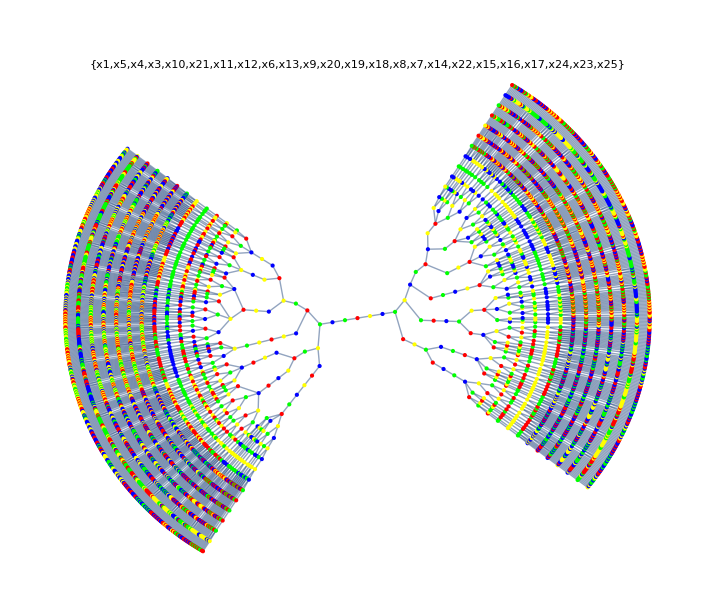

```mathematica
With[
{g=Graph[DeleteDuplicates[Flatten[edges]]]},
Graph[g, GraphLayout->"RadialDrawing",VertexSize->Large,VertexStyle->Map[#->IndexToColor[ FromDigits[ StringTake[#,-1]]]&, VertexList[g]],
PlotLabel->orderrrr]
]
```

```mathematica
Graph[Sort[DeleteDuplicates[Flatten[edges]]]]
```